# Solving The Schrödinger Equation for Finite Potential: from atoms to molecules to solids

Authors: Angel Salazar 
School of Physical Sciences and Nanotechnology

## Single Finite Potential Well: model of a single atom

We want to solve the time independent Schrödinger equation:
-ℏ^2/(2m) (∂^2 ψ(x))/(∂x) V(x)ψ(x) = E ψ(x)

Let’s define the finite potential.  use +pw+:

```mathematica
v[x_]:=Piecewise[{{v0, x<-a/2}, {0, -a/2≤x≤a/2}, {v0, x> a/2}}]
```

```mathematica
la = 2 (*bohr*);
vpot = 6.5 (*Subscript[E, h]*);
```

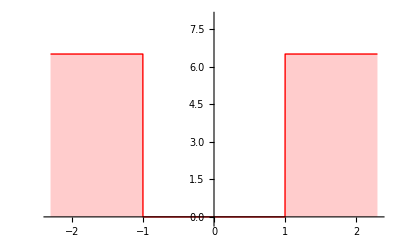

```mathematica
Plot[v[x]/.{v0->vpot,a->la},{x,-la-0.3,la+0.3}, 
AxesStyle->{"x","V(x)"},
PlotStyle->{Red,Thick},
PlotRange->{Automatic,{-0.2,vpot+1.5}},
AxesStyle->Arrowheads[{0.0,0.03}],
Filling->Axis
]
```

### Solving the Schrödinger equation in a . u .

In atomic units, ℏ -> 1, m -> 1, e -> 1; then the lengths are given in Bohr, 1bohr= 0.53 Å, and the energy in Hartree E_h = 27.21 eV. 
Let’s define α = √(2(v0 - ℰ)), β = √(2 ℰ),   (ℰ is +scE+)

```mathematica
Do[Subscript[c,i]=.,{i,4}];
Do[Subscript[ϕ,i]=.,{i,3}];
Subscript[ϕ, 1][x_]:=Subscript[c, 1] Exp[α x];
Subscript[ϕ, 2][x_]:=Subscript[c, 2] Cos[β x] + Subscript[c, 3] Sin[β x];
Subscript[ϕ, 3][x_]:=Subscript[c, 4] Exp[-α x];
```

Unset::norep: Assignment on Subscript for c_1 not found.

Unset::norep: Assignment on Subscript for c_2 not found.

Unset::norep: Assignment on Subscript for c_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

Unset::norep: Assignment on Subscript for ϕ_1 not found.

Unset::norep: Assignment on Subscript for ϕ_2 not found.

Unset::norep: Assignment on Subscript for ϕ_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

Let’s define the wavefunction  φ, φ is +j+:

```mathematica
φ[x_]:=Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2≤x≤a/2}, {Subscript[ϕ, 3][x], x> a/2}}]
```

Now we need to consider the boundary conditions

```mathematica
eq[1]=(Subscript[ϕ, 1][x]-Subscript[ϕ, 2][x]/.x->-a/2)==0
eq[2]=(Subscript[ϕ, 1]'[x]-Subscript[ϕ, 2]'[x]/.x->-a/2)==0
eq[3]=(Subscript[ϕ, 2][x]-Subscript[ϕ, 3][x]/.x->a/2)==0
eq[4]=(Subscript[ϕ, 2]'[x]-Subscript[ϕ, 3]'[x]/.x->a/2)==0
```

ⅇ^(-(a α)/2) c_1-Cos[(a β)/2] c_2+Sin[(a β)/2] c_3==0

ⅇ^(-(a α)/2) α c_1-β Sin[(a β)/2] c_2-β Cos[(a β)/2] c_3==0

Cos[(a β)/2] c_2+Sin[(a β)/2] c_3-ⅇ^(-(a α)/2) c_4==0

-β Sin[(a β)/2] c_2+β Cos[(a β)/2] c_3+ⅇ^(-(a α)/2) α c_4==0

```mathematica
mat = CoefficientArrays[Table[eq[i],{i,4}],Table[Subscript[c, i],{i,4}]][[2]]//Normal
```

{{ⅇ^(-(a α)/2),-Cos[(a β)/2],Sin[(a β)/2],0},{ⅇ^(-(a α)/2) α,-β Sin[(a β)/2],-β Cos[(a β)/2],0},{0,Cos[(a β)/2],Sin[(a β)/2],-ⅇ^(-(a α)/2)},{0,-β Sin[(a β)/2],β Cos[(a β)/2],ⅇ^(-(a α)/2) α}}

```mathematica
mat//MatrixForm
```

(ⅇ^(-(a α)/2) | -Cos[(a β)/2] | Sin[(a β)/2] | 0
ⅇ^(-(a α)/2) α | -β Sin[(a β)/2] | -β Cos[(a β)/2] | 0
0 | Cos[(a β)/2] | Sin[(a β)/2] | -ⅇ^(-(a α)/2)
0 | -β Sin[(a β)/2] | β Cos[(a β)/2] | ⅇ^(-(a α)/2) α)

```mathematica
mat2 = (mat/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)})/.{v0->vpot, a->la}//FullSimplify
```

{{ⅇ^(-1.41421 √(6.5-ℰ)),-Cos[√2 √ℰ],Sin[√2 √ℰ],0},{1.41421 ⅇ^(-1.41421 √(6.5-ℰ)) √(6.5-ℰ),-√2 √ℰ Sin[√2 √ℰ],-√2 √ℰ Cos[√2 √ℰ],0},{0,Cos[√2 √ℰ],Sin[√2 √ℰ],-ⅇ^(-1.41421 √(6.5-ℰ))},{0,-√2 √ℰ Sin[√2 √ℰ],√2 √ℰ Cos[√2 √ℰ],1.41421 ⅇ^(-1.41421 √(6.5-ℰ)) √(6.5-ℰ)}}

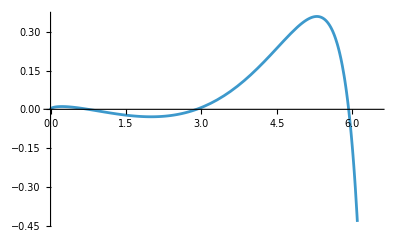

```mathematica
Plot[Det[mat2],{ℰ,0,vpot}]
```

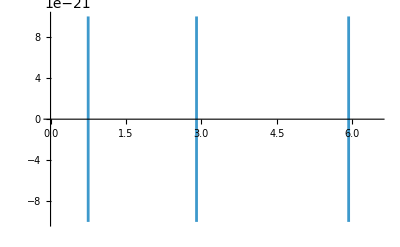

```mathematica
fig = Plot[Det[mat2],{ℰ,0,vpot},PlotRange->{-10^-20,10^-20}]
```

```mathematica
Short[fig,5]
```

-Graphics-

```mathematica
fig[[1,1,1,1,1,3,1]][[2;;-1]]
```

{Line[{{0.748476,1.×10^-20},{0.748476,-1.×10^-20}}],Line[{{2.9027,-1.×10^-20},{2.9027,1.×10^-20}}],Line[{{5.92702,1.×10^-20},{5.92702,-1.×10^-20}}]}

```mathematica
approxroot1=fig[[1,1,1,1,1,3,1]][[2;;-1]]//Map[#[[1,1,1]]&,#]&//Sort
```

{0.748476,2.9027,5.92702}

```mathematica
rval1=approxroot1//Map[FindRoot[Det[mat2],{ℰ,#}]&,#]&//Map[ℰ/.#&,#]&
```

{0.7495,2.9032,5.92714}

```mathematica
fig[[1,1,1]]
```

{{{{},{},{Directive[Opacity[1.],RGBColor[0.24, 0.6, 0.8],AbsoluteThickness[2]],Line[{{0.748476,1.×10^-20},{0.748476,-1.×10^-20}}],Line[{{2.9027,-1.×10^-20},{2.9027,1.×10^-20}}],Line[{{5.92702,1.×10^-20},{5.92702,-1.×10^-20}}]}}},{}}

```mathematica
g=Normal[fig];  

(*extract the x of every vertical line the plot drew (your zero crossings)*)
aproxroot=Sort@Cases[g,Line[{{x_,y1_},{x_,y2_}}]:>x,Infinity]
```

{0.748476,2.9027,5.92702}

```mathematica
rval = aproxroot//Map[FindRoot[Det[mat2],{ℰ,#}]&,#]&//Map[ℰ/.# &,#]&
```

{0.7495,2.9032,5.92714}

### Level 1

```mathematica
nval = 1;
Do[Subscript[c,i]=.,{i,4}];
Evaluate[Table[Subscript[c, i],{i,4}]]=(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

Unset::norep: Assignment on Subscript for c_1 not found.

Unset::norep: Assignment on Subscript for c_2 not found.

Unset::norep: Assignment on Subscript for c_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

{0.705376,0.0699299,0,0.705376}

We need to find the normalization constant for φ(x) , ∞

```mathematica
int =NIntegrate[Abs[φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

0.00633217

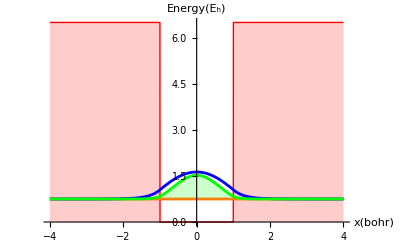

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int) φ[x],
ℰ+(1/(√int) φ[x])^2

}/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,
{x,-la-2,la+2},
PlotRange->All,
AxesLabel->{"x(bohr)","Energy(E_h)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
PlotStyle->{{Red,Thick},Orange, Blue, Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}

]
```

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron when x>a/2?

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,la/2,∞}]
```

0.0131291

Let' s find the Δx, then we need the expected value of ⟨x⟩ and ⟨x^2⟩

```mathematica
⟨x⟩=NIntegrate[1/(√int)φ[x]*x 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.0000000179351824814857839113022984732213743311998205226198868701}. NIntegrate obtained 7.67615×10^-17 and 1.60643×10^-14 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)φ[x]*x^2 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

0.228641

Then the Δx is :

```mathematica
Δx = √(⟨x^2⟩-⟨x⟩^2)
```

0.478165

Now let' s find the uncertainty in the momentum Δp :

```mathematica
⟨p⟩=NIntegrate[1/(√int)φ[x]**-ⅈ D[1/(√int)φ[x],x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.667984}. NIntegrate obtained 0.+2.28116×10^-16 ⅈ and 9.95236×10^-17 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)φ[x]*(-D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

1.15764

Then Δp is

```mathematica
Δp =  √(⟨p^2⟩-⟨p⟩^2)
```

1.07594

Therefore the Heisengerg uncertainty Δx Δp is:

```mathematica
Δx Δp
```

0.514476

What is the expected value of the kinetic energy k = -ℏ^2/(2m)

```mathematica
⟨Subscript[k, nval]⟩=NIntegrate[1/(√int)φ[x]*(-1/2 D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

0.578822

What is the expected potential energy for this level?

```mathematica
⟨Subscript[U, nval]⟩=NIntegrate[1/(√int)φ[x]*v[x]  1/(√int) φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

0.170678

Now, check this out: The total energy of the level

```mathematica
Subscript[E1, tot1]=⟨Subscript[k, nval]⟩+⟨Subscript[U, nval]⟩
```

0.7495

```mathematica
ℰ/.ℰ->rval[[nval]]
```

0.7495

### Level 2

```mathematica
nval = 2;
Do[Subscript[c,i]=.,{i,4}];
Evaluate[Table[Subscript[c, i],{i,4}]]=(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{-0.705261,0,0.0722025,0.705261}

We need to find the normalization constant for φ(x) , ∞

```mathematica
int =NIntegrate[Abs[φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

0.00715691

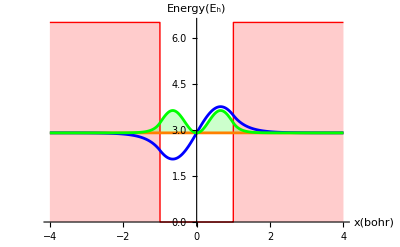

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int) φ[x],
ℰ+(1/(√int) φ[x])^2

}/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,
{x,-la-2,la+2},
PlotRange->All,
AxesLabel->{"x(bohr)","Energy(E_h)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
PlotStyle->{{Red,Thick},Orange, Blue, Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron when x>a/2?

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,la/2,∞}]
```

0.0606513

Let' s find the Δx, then we need the expected value of ⟨x⟩ and ⟨x^2⟩

```mathematica
⟨x⟩=NIntegrate[1/(√int)φ[x]*x 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.9999999641296356803699999546324928868801240611219327547587454319}. NIntegrate obtained 2.15106×10^-16 and 1.46294×10^-13 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)φ[x]*x^2 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

0.548414

Then the Δx is :

```mathematica
Δx = √(⟨x^2⟩-⟨x⟩^2)
```

0.74055

Now let' s find the uncertainty in the momentum Δp :

```mathematica
⟨p⟩=NIntegrate[1/(√int)φ[x]**-ⅈ D[1/(√int)φ[x],x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-1.0000000179351824814857839113022984732213743311998205226198868701}. NIntegrate obtained 0.+4.38885×10^-16 ⅈ and 1.58363×10^-13 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)φ[x]*(-D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

4.22948

Then Δp is

```mathematica
Δp =  √(⟨p^2⟩-⟨p⟩^2)
```

2.05657

Therefore the Heisengerg uncertainty Δx Δp is:

```mathematica
Δx Δp
```

1.52299

What is the expected value of the kinetic energy k = -ℏ^2/(2m)

```mathematica
⟨Subscript[k, nval]⟩=NIntegrate[1/(√int)φ[x]*(-1/2 D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

2.11474

What is the expected potential energy for this level?

```mathematica
⟨Subscript[U, nval]⟩=NIntegrate[1/(√int)φ[x]*v[x]  1/(√int) φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

0.788467

Now, check this out: The total energy of the level

```mathematica
Subscript[E1, tot2]=⟨Subscript[k, nval]⟩+⟨Subscript[U, nval]⟩
```

2.9032

```mathematica
ℰ/.ℰ->rval[[nval]]
```

2.9032

### Level 3

```mathematica
nval = 3;
Do[Subscript[c,i]=.,{i,4}];
Evaluate[Table[Subscript[c, i],{i,4}]]=(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{0.685361,-0.24609,0,0.685361}

We need to find the normalization constant for φ(x) , ∞

```mathematica
int =NIntegrate[Abs[φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

0.117138

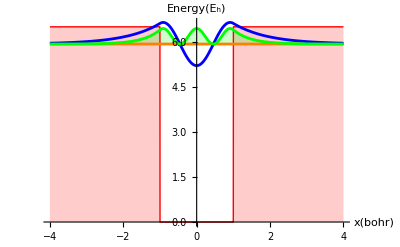

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int) φ[x],
ℰ+(1/(√int) φ[x])^2

}/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,
{x,-la-2,la+2},
PlotRange->All,
AxesLabel->{"x(bohr)","Energy(E_h)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
PlotStyle->{{Red,Thick},Orange, Blue, Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron when x>a/2?

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,la/2,∞}]
```

0.220218

Let' s find the Δx, then we need the expected value of ⟨x⟩ and ⟨x^2⟩

```mathematica
⟨x⟩=NIntegrate[1/(√int)φ[x]*x 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.77168}. NIntegrate obtained -1.10589×10^-15 and 7.27872×10^-17 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)φ[x]*x^2 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

1.27519

Then the Δx is :

```mathematica
Δx = √(⟨x^2⟩-⟨x⟩^2)
```

1.12924

Now let' s find the uncertainty in the momentum Δp :

```mathematica
⟨p⟩=NIntegrate[1/(√int)φ[x]**-ⅈ D[1/(√int)φ[x],x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.99999998206481784018499997731624644344006203056096637737937271595}. NIntegrate obtained 0.-8.06646×10^-16 ⅈ and 9.10127×10^-14 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)φ[x]*(-D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

6.12863

Then Δp is

```mathematica
Δp =  √(⟨p^2⟩-⟨p⟩^2)
```

2.47561

Therefore the Heisengerg uncertainty Δx Δp is:

```mathematica
Δx Δp
```

2.79556

What is the expected value of the kinetic energy k = -ℏ^2/(2m)

```mathematica
⟨Subscript[k, nval]⟩=NIntegrate[1/(√int)φ[x]*(-1/2 D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

3.06431

What is the expected potential energy for this level?

```mathematica
⟨Subscript[U, nval]⟩=NIntegrate[1/(√int)φ[x]*v[x]  1/(√int) φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

2.86283

Now, check this out: The total energy of the level

```mathematica
Subscript[E1, tot3]=⟨Subscript[k, nval]⟩+⟨Subscript[U, nval]⟩
```

5.92714

```mathematica
ℰ/.ℰ->rval[[nval]]
```

5.92714

### Summary of the plots

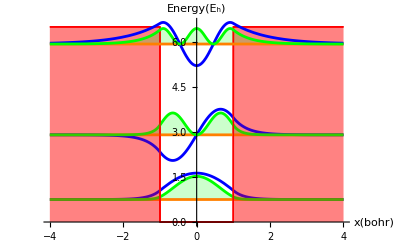

```mathematica
Show@@Table[figure[i],{i,3}]
```

What is the total energy of the system if it has 3 ⅇ?

```mathematica
Subscript[E, tot][atom] = 2 rval[[1]]+rval[[2]]
```

4.40221

```mathematica
Subscript[k, tot]= 2*⟨Subscript[k, 1]⟩+ ⟨Subscript[k, 2]⟩
```

3.27238

```mathematica
Subscript[u, tot] =2*⟨Subscript[U, 1]⟩+⟨Subscript[U, 2]⟩
```

1.12982

## Two Finite Potential Well: model of a molecule

We want to solve the time independent Schrödinger equation:
-ℏ^2/(2m) (∂^2 ψ(x))/(∂x) V(x)ψ(x) = E ψ(x)

### Define the potential

Let’s define the finite potential.  use +pw+:

```mathematica
v[x_]:=Piecewise[{{v0, x<-b/2-a}, {0, -b/2-a≤x≤-b/2}, {v0, -b/2≤x≤b/2}, {0, b/2≤x≤b/2+a}, {v0, x> b+a/2}}]
```

```mathematica
la = 2 (*bohr*);
lb = 1 (*bohr*);
vpot = 6.5 (*Subscript[E, h]*);
```

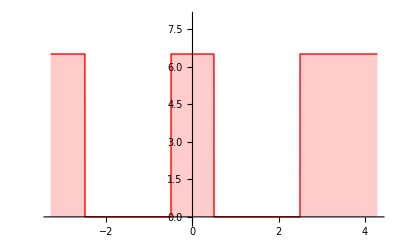

```mathematica
Plot[v[x]/.{v0->vpot,a->la,b->lb},{x,-la-lb-0.3,la+la+0.3}, 
AxesStyle->{"x","V(x)"},
PlotStyle->{Red,Thick},
PlotRange->{Automatic,{-0.2,vpot+1.5}},
AxesStyle->Arrowheads[{0.0,0.03}],
Filling->Axis
]
```

### Solving the Schrödinger equation in a . u .

In atomic units, ℏ -> 1, m -> 1, e -> 1; then the lengths are given in Bohr, 1bohr= 0.53 Å, and the energy in Hartree E_h = 27.21 eV. 
Let’s define α = √(2(v0 - ℰ)), β = √(2 ℰ),   (ℰ is +scE+)

```mathematica
Do[Subscript[c,i]=.,{i,8}];
Do[Subscript[ϕ,i]=.,{i,5}];
Subscript[ϕ, 1][x_]:=Subscript[c, 1] Exp[α x];
Subscript[ϕ, 2][x_]:=Subscript[c, 2] Cos[β x] + Subscript[c, 3] Sin[β x];
Subscript[ϕ, 3][x_]:=Subscript[c, 4] Exp[-α x]+Subscript[c, 5] Exp[α x];
Subscript[ϕ, 4][x_]:=Subscript[c, 6] Cos[β x] + Subscript[c, 7] Sin[β x];
Subscript[ϕ, 5][x_]:=Subscript[c, 8] Exp[-α x]
```

Unset::norep: Assignment on Subscript for c_5 not found.

Unset::norep: Assignment on Subscript for c_6 not found.

Unset::norep: Assignment on Subscript for c_7 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

Unset::norep: Assignment on Subscript for ϕ_1 not found.

Unset::norep: Assignment on Subscript for ϕ_2 not found.

Unset::norep: Assignment on Subscript for ϕ_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

Let’s define the wavefunction  φ, φ is +j+:

```mathematica
φ[x_]:=Piecewise[{{Subscript[ϕ, 1][x], x<-b/2-a}, {Subscript[ϕ, 2][x], -b/2-a≤x≤-b/2}, {Subscript[ϕ, 3][x], -b/2≤x≤b/2}, {Subscript[ϕ, 4][x], b/2≤x≤b/2+a}, {Subscript[ϕ, 5][x], x> b+a/2}}]
```

Now we need to consider the boundary conditions

```mathematica
eq[1]=(Subscript[ϕ, 1][x]-Subscript[ϕ, 2][x]/.x->-b/2-a)==0
eq[2]=(Subscript[ϕ, 1]'[x]-Subscript[ϕ, 2]'[x]/.x->-b/2-a)==0
eq[3]=(Subscript[ϕ, 2][x]-Subscript[ϕ, 3][x]/.x->-b/2)==0
eq[4]=(Subscript[ϕ, 2]'[x]-Subscript[ϕ, 3]'[x]/.x->-b/2)==0
eq[5]=(Subscript[ϕ, 3][x]-Subscript[ϕ, 4][x]/.x->b/2)==0
eq[6]=(Subscript[ϕ, 3]'[x]-Subscript[ϕ, 4]'[x]/.x->b/2)==0
eq[7]=(Subscript[ϕ, 4][x]-Subscript[ϕ, 5][x]/.x->b/2+a)==0
eq[8]=(Subscript[ϕ, 4]'[x]-Subscript[ϕ, 5]'[x]/.x->b/2+a)==0
```

ⅇ^((-a-b/2) α) c_1-Cos[(-a-b/2) β] c_2-Sin[(-a-b/2) β] c_3==0

ⅇ^((-a-b/2) α) α c_1+β Sin[(-a-b/2) β] c_2-β Cos[(-a-b/2) β] c_3==0

Cos[(b β)/2] c_2-Sin[(b β)/2] c_3-ⅇ^((b α)/2) c_4-ⅇ^(-(b α)/2) c_5==0

β Sin[(b β)/2] c_2+β Cos[(b β)/2] c_3+ⅇ^((b α)/2) α c_4-ⅇ^(-(b α)/2) α c_5==0

ⅇ^(-(b α)/2) c_4+ⅇ^((b α)/2) c_5-Cos[(b β)/2] c_6-Sin[(b β)/2] c_7==0

-ⅇ^(-(b α)/2) α c_4+ⅇ^((b α)/2) α c_5+β Sin[(b β)/2] c_6-β Cos[(b β)/2] c_7==0

Cos[(a+b/2) β] c_6+Sin[(a+b/2) β] c_7-ⅇ^(-((a+b/2) α)) c_8==0

-β Sin[(a+b/2) β] c_6+β Cos[(a+b/2) β] c_7+ⅇ^(-((a+b/2) α)) α c_8==0

```mathematica
mat = CoefficientArrays[Table[eq[i],{i,8}],Table[Subscript[c, i],{i,8}]][[2]]//Normal
```

{{ⅇ^((-a-b/2) α),-Cos[(-a-b/2) β],-Sin[(-a-b/2) β],0,0,0,0,0},{ⅇ^((-a-b/2) α) α,β Sin[(-a-b/2) β],-β Cos[(-a-b/2) β],0,0,0,0,0},{0,Cos[(b β)/2],-Sin[(b β)/2],-ⅇ^((b α)/2),-ⅇ^(-(b α)/2),0,0,0},{0,β Sin[(b β)/2],β Cos[(b β)/2],ⅇ^((b α)/2) α,-ⅇ^(-(b α)/2) α,0,0,0},{0,0,0,ⅇ^(-(b α)/2),ⅇ^((b α)/2),-Cos[(b β)/2],-Sin[(b β)/2],0},{0,0,0,-ⅇ^(-(b α)/2) α,ⅇ^((b α)/2) α,β Sin[(b β)/2],-β Cos[(b β)/2],0},{0,0,0,0,0,Cos[(a+b/2) β],Sin[(a+b/2) β],-ⅇ^(-((a+b/2) α))},{0,0,0,0,0,-β Sin[(a+b/2) β],β Cos[(a+b/2) β],ⅇ^(-((a+b/2) α)) α}}

```mathematica
mat//MatrixForm
```

(ⅇ^((-a-b/2) α) | -Cos[(-a-b/2) β] | -Sin[(-a-b/2) β] | 0 | 0 | 0 | 0 | 0
ⅇ^((-a-b/2) α) α | β Sin[(-a-b/2) β] | -β Cos[(-a-b/2) β] | 0 | 0 | 0 | 0 | 0
0 | Cos[(b β)/2] | -Sin[(b β)/2] | -ⅇ^((b α)/2) | -ⅇ^(-(b α)/2) | 0 | 0 | 0
0 | β Sin[(b β)/2] | β Cos[(b β)/2] | ⅇ^((b α)/2) α | -ⅇ^(-(b α)/2) α | 0 | 0 | 0
0 | 0 | 0 | ⅇ^(-(b α)/2) | ⅇ^((b α)/2) | -Cos[(b β)/2] | -Sin[(b β)/2] | 0
0 | 0 | 0 | -ⅇ^(-(b α)/2) α | ⅇ^((b α)/2) α | β Sin[(b β)/2] | -β Cos[(b β)/2] | 0
0 | 0 | 0 | 0 | 0 | Cos[(a+b/2) β] | Sin[(a+b/2) β] | -ⅇ^(-((a+b/2) α))
0 | 0 | 0 | 0 | 0 | -β Sin[(a+b/2) β] | β Cos[(a+b/2) β] | ⅇ^(-((a+b/2) α)) α)

```mathematica
mat2 = (mat/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)})/.{v0->vpot, a->la,b->lb}//FullSimplify
```

{{ⅇ^(-5 √(3.25-0.5 ℰ)),-Cos[(5 √ℰ)/(√2)],Sin[(5 √ℰ)/(√2)],0,0,0,0,0},{1.41421 ⅇ^(-5 √(3.25-0.5 ℰ)) √(6.5-ℰ),-√2 √ℰ Sin[(5 √ℰ)/(√2)],-√2 √ℰ Cos[(5 √ℰ)/(√2)],0,0,0,0,0},{0,Cos[(√ℰ)/(√2)],-Sin[(√ℰ)/(√2)],-ⅇ^(√(3.25-0.5 ℰ)),-ⅇ^(-√(3.25-0.5 ℰ)),0,0,0},{0,√2 √ℰ Sin[(√ℰ)/(√2)],√2 √ℰ Cos[(√ℰ)/(√2)],1.41421 ⅇ^(√(3.25-0.5 ℰ)) √(6.5-ℰ),-1.41421 ⅇ^(-√(3.25-0.5 ℰ)) √(6.5-ℰ),0,0,0},{0,0,0,ⅇ^(-√(3.25-0.5 ℰ)),ⅇ^(√(3.25-0.5 ℰ)),-Cos[(√ℰ)/(√2)],-Sin[(√ℰ)/(√2)],0},{0,0,0,-1.41421 ⅇ^(-√(3.25-0.5 ℰ)) √(6.5-ℰ),1.41421 ⅇ^(√(3.25-0.5 ℰ)) √(6.5-ℰ),√2 √ℰ Sin[(√ℰ)/(√2)],-√2 √ℰ Cos[(√ℰ)/(√2)],0},{0,0,0,0,0,Cos[(5 √ℰ)/(√2)],Sin[(5 √ℰ)/(√2)],-ⅇ^(-5 √(3.25-0.5 ℰ))},{0,0,0,0,0,-√2 √ℰ Sin[(5 √ℰ)/(√2)],√2 √ℰ Cos[(5 √ℰ)/(√2)],1.41421 ⅇ^(-5 √(3.25-0.5 ℰ)) √(6.5-ℰ)}}

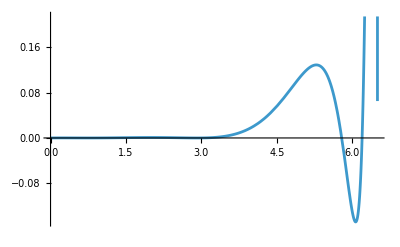

```mathematica
Plot[Det[mat2],{ℰ,0,vpot}]
```

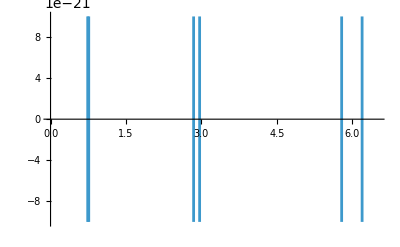

```mathematica
fig = Plot[Det[mat2],{ℰ,0,vpot},PlotRange->{-10^-20,10^-20}]
```

```mathematica
fig[[1,1,1,1,1,3,1]][[2;;-1]]
```

{Line[{{5.78811,1.×10^-20},{5.78811,-1.×10^-20}}],Line[{{0.739199,1.×10^-20},{0.739199,-1.×10^-20}}],Line[{{6.19469,-1.×10^-20},{6.19469,1.×10^-20}}],Line[{{0.7595,-1.×10^-20},{0.7595,1.×10^-20}}],Line[{{2.84476,1.×10^-20},{2.84476,-1.×10^-20}}],Line[{{2.96416,-1.×10^-20},{2.96416,1.×10^-20}}]}

```mathematica
approxroot=fig[[1,1,1,1,1,3,1]][[2;;-1]]//Map[#[[1,1,1]]&,#]&//Sort
```

{0.739199,0.7595,2.84476,2.96416,5.78811,6.19469}

```mathematica
rval=approxroot//Map[FindRoot[Det[mat2],{ℰ,#}]&,#]&//Map[ℰ/.#&,#]&
```

{0.739194,0.759528,2.84474,2.96417,5.78909,6.19471}

```mathematica
fig[[1,1,1]]
```

{{{{},{},{Directive[Opacity[1.],RGBColor[0.24, 0.6, 0.8],AbsoluteThickness[2]],Line[{{5.78811,1.×10^-20},{5.78811,-1.×10^-20}}],Line[{{0.739199,1.×10^-20},{0.739199,-1.×10^-20}}],Line[{{6.19469,-1.×10^-20},{6.19469,1.×10^-20}}],Line[{{0.7595,-1.×10^-20},{0.7595,1.×10^-20}}],Line[{{2.84476,1.×10^-20},{2.84476,-1.×10^-20}}],Line[{{2.96416,-1.×10^-20},{2.96416,1.×10^-20}}]}}},{}}

### Level 1

```mathematica
nval = 1;
Do[Subscript[c,i]=.,{i,8}];
Evaluate[Table[Subscript[c, i],{i,8}]]=(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

Unset::norep: Assignment on Subscript for c_1 not found.

Unset::norep: Assignment on Subscript for c_2 not found.

Unset::norep: Assignment on Subscript for c_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

{0.707107,-0.000103738,-0.000420087,0.0000274377,0.0000274377,-0.000103738,0.000420087,0.707107}

We need to find the normalization constant for φ(x) , ∞

```mathematica
int =NIntegrate[Abs[φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

4.8918×10^-7

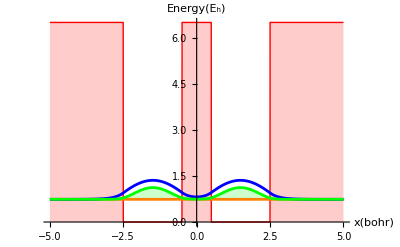

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int) φ[x],
ℰ+(1/(√int) φ[x])^2

}/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,
{x,-la-lb-2,la+lb+2},
PlotRange->All,
AxesLabel->{"x(bohr)","Energy(E_h)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
PlotStyle->{{Red,Thick},Orange, Blue, Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}

]
```

Here we can see the bounding state

For this first energy level we can see that there is no nodes, since we have two atoms the energy level splits, it is forming a bounding level. This is the origin of the covalent bond which is related with the tunneling effect, since in the forbidden region is non zero, so the electron can be found with probabilities to be in the left region or right region. The blue line is the wave function.

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron when x>a+b/2?

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-lb,lb}]
```

0.166753

Let' s find the Δx, then we need the expected value of ⟨x⟩ and ⟨x^2⟩

```mathematica
⟨x⟩=NIntegrate[1/(√int)φ[x]*x 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.5000000179351824814857839113022984732213743311998205226198868701}. NIntegrate obtained 1.00616×10^-10 and 1.93384×10^-14 for the integral and error estimates.

1.00616×10^-10

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)φ[x]*x^2 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

2.44961

Then the Δx is :

```mathematica
Δx = √(⟨x^2⟩-⟨x⟩^2)
```

1.56512

Now let' s find the uncertainty in the momentum Δp :

```mathematica
⟨p⟩=NIntegrate[1/(√int)φ[x]**-ⅈ D[1/(√int)φ[x],x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.5000000179351824814857839113022984732213743311998205226198868701}. NIntegrate obtained 0.+3.16205×10^-13 ⅈ and 2.5824×10^-14 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)φ[x]*(-D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

1.09625

Then Δp is

```mathematica
Δp =  √(⟨p^2⟩-⟨p⟩^2)
```

1.04702

Therefore the Heisengerg uncertainty Δx Δp is:

```mathematica
Δx Δp
```

1.63872

What is the expected value of the kinetic energy k = -ℏ^2/(2m)

```mathematica
⟨Subscript[k, nval]⟩=NIntegrate[1/(√int)φ[x]*(-1/2 D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

0.548126

What is the expected potential energy for this level?

```mathematica
⟨Subscript[U, nval]⟩=NIntegrate[1/(√int)φ[x]*v[x]  1/(√int) φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

0.191068

Now, check this out: The total energy of the level

```mathematica
Subscript[E2, tot1]=⟨Subscript[k, nval]⟩+⟨Subscript[U, nval]⟩
```

0.739194

```mathematica
ℰ/.ℰ->rval[[nval]]
```

0.739194

### Level 2

```mathematica
nval = 2;
Do[Subscript[c,i]=.,{i,8}];
Evaluate[Table[Subscript[c, i],{i,8}]]=(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{-0.707107,0.000123297,0.000415411,-0.0000265255,0.0000265255,-0.000123297,0.000415411,0.707107}

We need to find the normalization constant for φ(x) , ∞

```mathematica
int =NIntegrate[Abs[φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

4.82117×10^-7

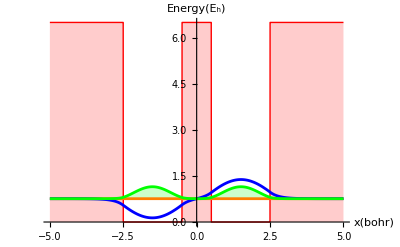

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int) φ[x],
ℰ+(1/(√int) φ[x])^2

}/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,
{x,-la-lb-2,la+lb+2},
PlotRange->All,
AxesLabel->{"x(bohr)","Energy(E_h)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
PlotStyle->{{Red,Thick},Orange, Blue, Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}

]
```

Here we can see the bounding state

For this first energy level we can see that there is no nodes, since we have two atoms the energy level splits, it is forming a bounding level. This is the origin of the covalent bond which is related with the tunneling effect, since in the forbidden region is non zero, so the electron can be found with probabilities to be in the left region or right region. The blue line is the wave function.

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron when x>a+b/2?

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-lb,lb}]
```

0.15074

Let' s find the Δx, then we need the expected value of ⟨x⟩ and ⟨x^2⟩

```mathematica
⟨x⟩=NIntegrate[1/(√int)φ[x]*x 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.5000000179351824814857839113022984732213743311998205226198868701}. NIntegrate obtained 1.32334×10^-10 and 2.02592×10^-14 for the integral and error estimates.

1.32334×10^-10

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)φ[x]*x^2 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

2.50693

Then the Δx is :

```mathematica
Δx = √(⟨x^2⟩-⟨x⟩^2)
```

1.58333

Now let' s find the uncertainty in the momentum Δp :

```mathematica
⟨p⟩=NIntegrate[1/(√int)φ[x]**-ⅈ D[1/(√int)φ[x],x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.4999999641296356803699999546324928868801240611219327547587454319}. NIntegrate obtained 0.-5.18855×10^-13 ⅈ and 6.71024×10^-14 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)φ[x]*(-D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

1.21675

Then Δp is

```mathematica
Δp =  √(⟨p^2⟩-⟨p⟩^2)
```

1.10306

Therefore the Heisengerg uncertainty Δx Δp is:

```mathematica
Δx Δp
```

1.74651

What is the expected value of the kinetic energy k = -ℏ^2/(2m)

```mathematica
⟨Subscript[k, nval]⟩=NIntegrate[1/(√int)φ[x]*(-1/2 D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

0.608376

What is the expected potential energy for this level?

```mathematica
⟨Subscript[U, nval]⟩=NIntegrate[1/(√int)φ[x]*v[x]  1/(√int) φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

0.151152

Now, check this out: The total energy of the level

```mathematica
Subscript[E2, tot2]=⟨Subscript[k, nval]⟩+⟨Subscript[U, nval]⟩
```

0.759528

```mathematica
ℰ/.ℰ->rval[[nval]]
```

0.759528

### Level 3

```mathematica
nval = 3;
Do[Subscript[c,i]=.,{i,8}];
Evaluate[Table[Subscript[c, i],{i,8}]]=(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{0.707106,0.000486012,0.00114043,-0.00021351,-0.00021351,0.000486012,-0.00114043,0.707106}

We need to find the normalization constant for φ(x) , ∞

```mathematica
int =NIntegrate[Abs[φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

4.30598×10^-6

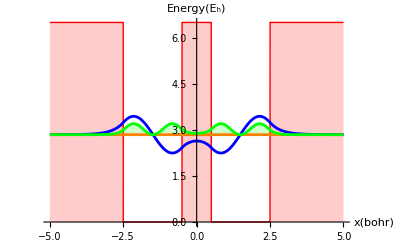

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int) φ[x],
ℰ+(1/(√int) φ[x])^2

}/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,
{x,-la-lb-2,la+lb+2},
PlotRange->All,
AxesLabel->{"x(bohr)","Energy(E_h)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
PlotStyle->{{Red,Thick},Orange, Blue, Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}

]
```

Here we can see the bounding state

For this first energy level we can see that there is no nodes, since we have two atoms the energy level splits, it is forming a bounding level. This is the origin of the covalent bond which is related with the tunneling effect, since in the forbidden region is non zero, so the electron can be found with probabilities to be in the left region or right region. The blue line is the wave function.

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron when x>a+b/2?

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-lb,lb}]
```

0.387518

Let' s find the Δx, then we need the expected value of ⟨x⟩ and ⟨x^2⟩

```mathematica
⟨x⟩=NIntegrate[1/(√int)φ[x]*x 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.5000000179351824814857839113022984732213743311998205226198868701}. NIntegrate obtained -4.7071×10^-12 and 7.1623×10^-14 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)φ[x]*x^2 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

2.73146

Then the Δx is :

```mathematica
Δx = √(⟨x^2⟩-⟨x⟩^2)
```

1.65271

Now let' s find the uncertainty in the momentum Δp :

```mathematica
⟨p⟩=NIntegrate[1/(√int)φ[x]**-ⅈ D[1/(√int)φ[x],x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-2.4999999641296356803699999546324928868801240611219327547587454319}. NIntegrate obtained 0.-1.24428×10^-13 ⅈ and 1.91099×10^-13 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)φ[x]*(-D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

3.90633

Then Δp is

```mathematica
Δp =  √(⟨p^2⟩-⟨p⟩^2)
```

1.97644

Therefore the Heisengerg uncertainty Δx Δp is:

```mathematica
Δx Δp
```

3.26649

What is the expected value of the kinetic energy k = -ℏ^2/(2m)

```mathematica
⟨Subscript[k, nval]⟩=NIntegrate[1/(√int)φ[x]*(-1/2 D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

1.95317

What is the expected potential energy for this level?

```mathematica
⟨Subscript[U, nval]⟩=NIntegrate[1/(√int)φ[x]*v[x]  1/(√int) φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

0.891571

Now, check this out: The total energy of the level

```mathematica
Subscript[E2, tot3]=⟨Subscript[k, nval]⟩+⟨Subscript[U, nval]⟩
```

2.84474

```mathematica
ℰ/.ℰ->rval[[nval]]
```

2.84474

### Level 4

```mathematica
nval = 4;
Do[Subscript[c,i]=.,{i,8}];
Evaluate[Table[Subscript[c, i],{i,8}]]=(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{-0.707105,-0.000704019,-0.00116066,0.000240478,-0.000240478,0.000704019,-0.00116066,0.707105}

We need to find the normalization constant for φ(x) , ∞

```mathematica
int =NIntegrate[Abs[φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

4.94077×10^-6

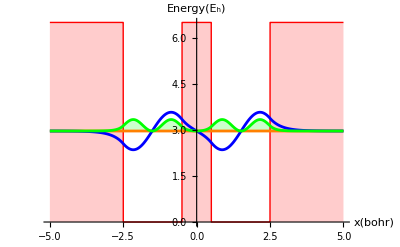

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int) φ[x],
ℰ+(1/(√int) φ[x])^2

}/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,
{x,-la-lb-2,la+lb+2},
PlotRange->All,
AxesLabel->{"x(bohr)","Energy(E_h)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
PlotStyle->{{Red,Thick},Orange, Blue, Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}

]
```

Here we can see the bounding state

For this first energy level we can see that there is no nodes, since we have two atoms the energy level splits, it is forming a bounding level. This is the origin of the covalent bond which is related with the tunneling effect, since in the forbidden region is non zero, so the electron can be found with probabilities to be in the left region or right region. The blue line is the wave function.

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron when x>a+b/2?

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-lb,lb}]
```

0.345875

Let' s find the Δx, then we need the expected value of ⟨x⟩ and ⟨x^2⟩

```mathematica
⟨x⟩=NIntegrate[1/(√int)φ[x]*x 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-2.4999999641296356803699999546324928868801240611219327547587454319}. NIntegrate obtained -2.84255×10^-13 and 1.87165×10^-13 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)φ[x]*x^2 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

2.87706

Then the Δx is :

```mathematica
Δx = √(⟨x^2⟩-⟨x⟩^2)
```

1.69619

Now let' s find the uncertainty in the momentum Δp :

```mathematica
⟨p⟩=NIntegrate[1/(√int)φ[x]**-ⅈ D[1/(√int)φ[x],x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.5000000358703643196300000453675071131198759388780672452412545681}. NIntegrate obtained 0.-2.50425×10^-14 ⅈ and 2.03758×10^-13 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)φ[x]*(-D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

4.58778

Then Δp is

```mathematica
Δp =  √(⟨p^2⟩-⟨p⟩^2)
```

2.14191

Therefore the Heisengerg uncertainty Δx Δp is:

```mathematica
Δx Δp
```

3.63309

What is the expected value of the kinetic energy k = -ℏ^2/(2m)

```mathematica
⟨Subscript[k, nval]⟩=NIntegrate[1/(√int)φ[x]*(-1/2 D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

2.29389

What is the expected potential energy for this level?

```mathematica
⟨Subscript[U, nval]⟩=NIntegrate[1/(√int)φ[x]*v[x]  1/(√int) φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

0.670283

Now, check this out: The total energy of the level

```mathematica
Subscript[E2, tot4]=⟨Subscript[k, nval]⟩+⟨Subscript[U, nval]⟩
```

2.96417

```mathematica
ℰ/.ℰ->rval[[nval]]
```

2.96417

### Level 5

```mathematica
nval = 5;
Do[Subscript[c,i]=.,{i,8}];
Evaluate[Table[Subscript[c, i],{i,8}]]=(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{0.705911,-0.0117825,-0.0360802,0.0157672,0.0157672,-0.0117825,0.0360802,0.705911}

We need to find the normalization constant for φ(x) , ∞

```mathematica
int =NIntegrate[Abs[φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

0.00528687

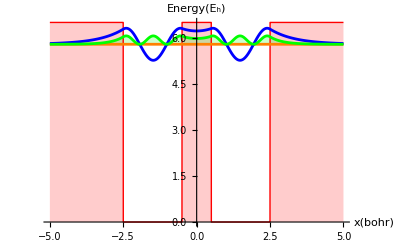

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int) φ[x],
ℰ+(1/(√int) φ[x])^2

}/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,
{x,-la-lb-2,la+lb+2},
PlotRange->All,
AxesLabel->{"x(bohr)","Energy(E_h)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
PlotStyle->{{Red,Thick},Orange, Blue, Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}

]
```

Here we can see the bounding state

For this first energy level we can see that there is no nodes, since we have two atoms the energy level splits, it is forming a bounding level. This is the origin of the covalent bond which is related with the tunneling effect, since in the forbidden region is non zero, so the electron can be found with probabilities to be in the left region or right region. The blue line is the wave function.

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron when x>a+b/2?

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-lb,lb}]
```

0.367109

Let' s find the Δx, then we need the expected value of ⟨x⟩ and ⟨x^2⟩

```mathematica
⟨x⟩=NIntegrate[1/(√int)φ[x]*x 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.5000000179351824814857839113022984732213743311998205226198868701}. NIntegrate obtained 1.11092×10^-14 and 1.17312×10^-13 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)φ[x]*x^2 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

3.37312

Then the Δx is :

```mathematica
Δx = √(⟨x^2⟩-⟨x⟩^2)
```

1.83661

Now let' s find the uncertainty in the momentum Δp :

```mathematica
⟨p⟩=NIntegrate[1/(√int)φ[x]**-ⅈ D[1/(√int)φ[x],x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.5000000358703643196300000453675071131198759388780672452412545681}. NIntegrate obtained 0.-2.94036×10^-15 ⅈ and 9.49047×10^-14 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)φ[x]*(-D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

6.17611

Then Δp is

```mathematica
Δp =  √(⟨p^2⟩-⟨p⟩^2)
```

2.48518

Therefore the Heisengerg uncertainty Δx Δp is:

```mathematica
Δx Δp
```

4.56429

What is the expected value of the kinetic energy k = -ℏ^2/(2m)

```mathematica
⟨Subscript[k, nval]⟩=NIntegrate[1/(√int)φ[x]*(-1/2 D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

3.08805

What is the expected potential energy for this level?

```mathematica
⟨Subscript[U, nval]⟩=NIntegrate[1/(√int)φ[x]*v[x]  1/(√int) φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

2.70104

Now, check this out: The total energy of the level

```mathematica
Subscript[E2, tot5]=⟨Subscript[k, nval]⟩+⟨Subscript[U, nval]⟩
```

5.78909

```mathematica
ℰ/.ℰ->rval[[nval]]
```

5.78909

### Level 6

```mathematica
nval = 6;
Do[Subscript[c,i]=.,{i,8}];
Evaluate[Table[Subscript[c, i],{i,8}]]=(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{-0.691614,0.0667736,0.0750336,-0.10762,0.10762,-0.0667736,0.0750336,0.691614}

We need to find the normalization constant for φ(x) , ∞

```mathematica
int =NIntegrate[Abs[φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

0.0367803

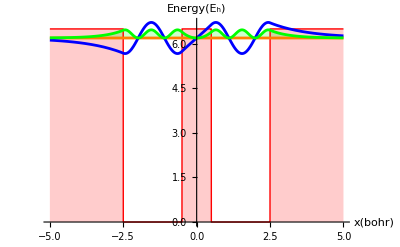

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int) φ[x],
ℰ+(1/(√int) φ[x])^2

}/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,
{x,-la-lb-2,la+lb+2},
PlotRange->All,
AxesLabel->{"x(bohr)","Energy(E_h)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
PlotStyle->{{Red,Thick},Orange, Blue, Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}

]
```

Here we can see the bounding state

For this first energy level we can see that there is no nodes, since we have two atoms the energy level splits, it is forming a bounding level. This is the origin of the covalent bond which is related with the tunneling effect, since in the forbidden region is non zero, so the electron can be found with probabilities to be in the left region or right region. The blue line is the wave function.

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron when x>a+b/2?

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-lb,lb}]
```

0.262557

Let' s find the Δx, then we need the expected value of ⟨x⟩ and ⟨x^2⟩

```mathematica
⟨x⟩=NIntegrate[1/(√int)φ[x]*x 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-2.293}. NIntegrate obtained 7.59288×10^-15 and 1.63497×10^-16 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)φ[x]*x^2 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

4.99442

Then the Δx is :

```mathematica
Δx = √(⟨x^2⟩-⟨x⟩^2)
```

2.23482

Now let' s find the uncertainty in the momentum Δp :

```mathematica
⟨p⟩=NIntegrate[1/(√int)φ[x]**-ⅈ D[1/(√int)φ[x],x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.5000000358703643196300000453675071131198759388780672452412545681}. NIntegrate obtained 0.+7.99708×10^-16 ⅈ and 2.10135×10^-13 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)φ[x]*(-D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

7.18132

Then Δp is

```mathematica
Δp =  √(⟨p^2⟩-⟨p⟩^2)
```

2.6798

Therefore the Heisengerg uncertainty Δx Δp is:

```mathematica
Δx Δp
```

5.98887

What is the expected value of the kinetic energy k = -ℏ^2/(2m)

```mathematica
⟨Subscript[k, nval]⟩=NIntegrate[1/(√int)φ[x]*(-1/2 D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

3.59066

What is the expected potential energy for this level?

```mathematica
⟨Subscript[U, nval]⟩=NIntegrate[1/(√int)φ[x]*v[x]  1/(√int) φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

2.60405

Now, check this out: The total energy of the level

```mathematica
Subscript[E2, tot6]=⟨Subscript[k, nval]⟩+⟨Subscript[U, nval]⟩
```

6.19471

```mathematica
ℰ/.ℰ->rval[[nval]]
```

6.19471

### Summary of the plots

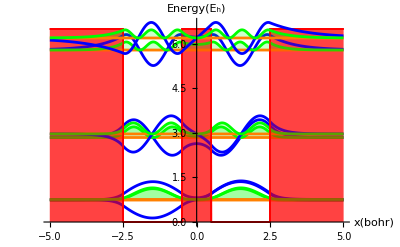

```mathematica
Show@@Table[figure[i],{i,6}]
```

What is the total energy of the system if it has 6 ⅇ?

What is the total energy of the system if it has 6 ⅇ

```mathematica
Etot6e[mol] = 2*(Subscript[E2, tot1]+Subscript[E2, tot2]+Subscript[E2, tot3])
```

8.68692

Kinetic energy of 6 ⅇ

```mathematica
Subscript[k, tot] =2(⟨Subscript[k, 1]⟩+⟨Subscript[k, 2]⟩+⟨Subscript[k, 3]⟩)
```

6.21933

Total potential energy of 6 ⅇ

```mathematica
Subscript[u, tot]=2 (⟨Subscript[U, 1]⟩+⟨Subscript[U, 2]⟩+⟨Subscript[U, 3]⟩)
```

2.46758

### Cohesion Energy

What is the cohesion energy for this 6 ⅇ system,  the cohesion energy is the energy needed to vaporize the system E_cohesion= Emol/2-Eatom.  What is the formation energy?

```mathematica
Subscript[E, cohesion6]=Etot6e[mol]/2-Subscript[E, tot][atom](*this Etot is for the single atom = 4,40221*)
```

-0.0587472

Now what would be the cohesion energy if each atom contributes with 4 ⅇ, then the molecule will have 8 ⅇ.

```mathematica
Subscript[E2, tot][atom]= 2(Subscript[E1, tot1]+Subscript[E1, tot2])
```

7.30541

```mathematica
Etot8e[mol] = 2*(Subscript[E2, tot1]+Subscript[E2, tot2]+Subscript[E2, tot3]+Subscript[E2, tot4])
```

14.6153

```mathematica
Subscript[E, cohesion8]=Etot8e[mol]/2-Subscript[E2, tot][atom]
```

0.00222281

Here we notice that  the system evaporates because the cohesion energy is positive meaning that E_atom< E_mol

Now what would be the cohesion energy if each atom contributes with 5 ⅇ, then the molecule will have 10 electrons

```mathematica
Subscript[E3, tot][atom]= 2(Subscript[E1, tot1]+Subscript[E1, tot2])+Subscript[E1, tot3]
```

13.2326

```mathematica
Etot10e[mol] = 2*(Subscript[E2, tot1]+Subscript[E2, tot2]+Subscript[E2, tot3]+Subscript[E2, tot4]+Subscript[E2, tot5])
```

26.1935

```mathematica
Subscript[E, cohesion10]=Etot10e[mol]/2-Subscript[E3, tot][atom]
```

-0.135827

Now we observe that the molecule is more stable.

## Three Finite Potential Well: model of a molecule

We want to solve the time independent Schrödinger equation:
-ℏ^2/(2m) (∂^2 ψ(x))/(∂x) V(x)ψ(x) = E ψ(x)

### Define the potential

Let’s define the finite potential.  use +pw+:

```mathematica
v[x_]:=Piecewise[{{v0, x<-2b-a}, {0, -2b-a≤x≤-a}, {v0, -a≤x≤-b}, {0, - b≤x≤b}, {v0, b≤x≤ +a}, {0, +a≤x≤2b+a}, {v0, x>2 b +a}}]
```

```mathematica
la = 2 (*bohr*);
lb = 1(*bohr*);
vpot = 6.5 (*Subscript[E, h]*);
```

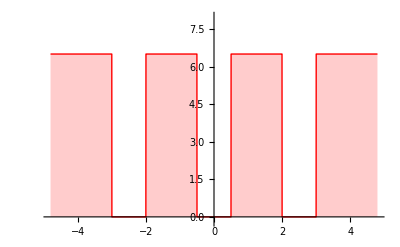

```mathematica
Plot[v[x]/.{v0->vpot,a->la,b->lb},{x,-2la-lb-0.3,+2la+lb+0.3}, 
AxesStyle->{"x","V(x)"},
PlotStyle->{Red,Thick},
PlotRange->{Automatic,{-0.2,vpot+1.5}},
AxesStyle->Arrowheads[{0.0,0.03}],
Filling->Axis
]
```

### Solving the Schrödinger equation in a . u .

In atomic units, ℏ -> 1, m -> 1, e -> 1; then the lengths are given in Bohr, 1bohr= 0.53 Å, and the energy in Hartree E_h = 27.21 eV. 
Let’s define α = √(2(v0 - ℰ)), β = √(2 ℰ),   (ℰ is +scE+)

```mathematica
Do[Subscript[c,i]=.,{i,12}];
Do[Subscript[ϕ,i]=.,{i,7}];
Subscript[ϕ, 1][x_]:=Subscript[c, 1] Exp[α x];
Subscript[ϕ, 2][x_]:=Subscript[c, 2] Cos[β x] + Subscript[c, 3] Sin[β x];
Subscript[ϕ, 3][x_]:=Subscript[c, 4] Exp[-α x]+Subscript[c, 5] Exp[α x];
Subscript[ϕ, 4][x_]:=Subscript[c, 6] Cos[β x] + Subscript[c, 7] Sin[β x];
Subscript[ϕ, 5][x_]:=Subscript[c, 8] Exp[-α x]+Subscript[c, 9] Exp[α x];
Subscript[ϕ, 6][x_]:=Subscript[c, 10] Cos[β x] + Subscript[c, 11] Sin[β x];
Subscript[ϕ, 7][x_]:=Subscript[c, 12] Exp[-α x];
```

Unset::norep: Assignment on Subscript for c_1 not found.

Unset::norep: Assignment on Subscript for c_2 not found.

Unset::norep: Assignment on Subscript for c_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

Unset::norep: Assignment on Subscript for ϕ_1 not found.

Unset::norep: Assignment on Subscript for ϕ_2 not found.

Unset::norep: Assignment on Subscript for ϕ_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

Let’s define the wavefunction  φ, φ is +j+:

```mathematica
φ[x_]:=Piecewise[{{Subscript[ϕ, 1][x], x<-2b-a}, {Subscript[ϕ, 2][x], -2b-a≤x≤-a}, {Subscript[ϕ, 3][x], -a≤x≤-b}, {Subscript[ϕ, 4][x], - b≤x≤b}, {Subscript[ϕ, 5][x], b≤x≤ +a}, {Subscript[ϕ, 6][x], +a≤x≤2b+a}, {Subscript[ϕ, 7][x], x>2 b +a}}]
```

Now we need to consider the boundary conditions

```mathematica
eq[1]=(Subscript[ϕ, 1][x]-Subscript[ϕ, 2][x]/.x->-2b-a)==0
eq[2]=(Subscript[ϕ, 1]'[x]-Subscript[ϕ, 2]'[x]/.x->-2b-a)==0
eq[3]=(Subscript[ϕ, 2][x]-Subscript[ϕ, 3][x]/.x->-a)==0
eq[4]=(Subscript[ϕ, 2]'[x]-Subscript[ϕ, 3]'[x]/.x->-a)==0
eq[5]=(Subscript[ϕ, 3][x]-Subscript[ϕ, 4][x]/.x->-b)==0
eq[6]=(Subscript[ϕ, 3]'[x]-Subscript[ϕ, 4]'[x]/.x->-b)==0
eq[7]=(Subscript[ϕ, 4][x]-Subscript[ϕ, 5][x]/.x->b)==0
eq[8]=(Subscript[ϕ, 4]'[x]-Subscript[ϕ, 5]'[x]/.x->b)==0
eq[9]=(Subscript[ϕ, 5][x]-Subscript[ϕ, 6][x]/.x->a)==0
eq[10]=(Subscript[ϕ, 5]'[x]-Subscript[ϕ, 6]'[x]/.x->a)==0
eq[11]=(Subscript[ϕ, 6][x]-Subscript[ϕ, 7][x]/.x->a+2b)==0
eq[12]=(Subscript[ϕ, 6]'[x]-Subscript[ϕ, 7]'[x]/.x->a+2b)==0
```

ⅇ^((-a-2 b) α) c_1-Cos[(-a-2 b) β] c_2-Sin[(-a-2 b) β] c_3==0

ⅇ^((-a-2 b) α) α c_1+β Sin[(-a-2 b) β] c_2-β Cos[(-a-2 b) β] c_3==0

Cos[a β] c_2-Sin[a β] c_3-ⅇ^(a α) c_4-ⅇ^(-a α) c_5==0

β Sin[a β] c_2+β Cos[a β] c_3+ⅇ^(a α) α c_4-ⅇ^(-a α) α c_5==0

ⅇ^(b α) c_4+ⅇ^(-b α) c_5-Cos[b β] c_6+Sin[b β] c_7==0

-ⅇ^(b α) α c_4+ⅇ^(-b α) α c_5-β Sin[b β] c_6-β Cos[b β] c_7==0

Cos[b β] c_6+Sin[b β] c_7-ⅇ^(-b α) c_8-ⅇ^(b α) c_9==0

-β Sin[b β] c_6+β Cos[b β] c_7+ⅇ^(-b α) α c_8-ⅇ^(b α) α c_9==0

ⅇ^(-a α) c_8+ⅇ^(a α) c_9-Cos[a β] c_10-Sin[a β] c_11==0

-ⅇ^(-a α) α c_8+ⅇ^(a α) α c_9+β Sin[a β] c_10-β Cos[a β] c_11==0

Cos[(a+2 b) β] c_10+Sin[(a+2 b) β] c_11-ⅇ^(-((a+2 b) α)) c_12==0

-β Sin[(a+2 b) β] c_10+β Cos[(a+2 b) β] c_11+ⅇ^(-((a+2 b) α)) α c_12==0

```mathematica
mat = CoefficientArrays[Table[eq[i],{i,12}],Table[Subscript[c, i],{i,12}]][[2]]//Normal
```

{{ⅇ^((-a-2 b) α),-Cos[(-a-2 b) β],-Sin[(-a-2 b) β],0,0,0,0,0,0,0,0,0},{ⅇ^((-a-2 b) α) α,β Sin[(-a-2 b) β],-β Cos[(-a-2 b) β],0,0,0,0,0,0,0,0,0},{0,Cos[a β],-Sin[a β],-ⅇ^(a α),-ⅇ^(-a α),0,0,0,0,0,0,0},{0,β Sin[a β],β Cos[a β],ⅇ^(a α) α,-ⅇ^(-a α) α,0,0,0,0,0,0,0},{0,0,0,ⅇ^(b α),ⅇ^(-b α),-Cos[b β],Sin[b β],0,0,0,0,0},{0,0,0,-ⅇ^(b α) α,ⅇ^(-b α) α,-β Sin[b β],-β Cos[b β],0,0,0,0,0},{0,0,0,0,0,Cos[b β],Sin[b β],-ⅇ^(-b α),-ⅇ^(b α),0,0,0},{0,0,0,0,0,-β Sin[b β],β Cos[b β],ⅇ^(-b α) α,-ⅇ^(b α) α,0,0,0},{0,0,0,0,0,0,0,ⅇ^(-a α),ⅇ^(a α),-Cos[a β],-Sin[a β],0},{0,0,0,0,0,0,0,-ⅇ^(-a α) α,ⅇ^(a α) α,β Sin[a β],-β Cos[a β],0},{0,0,0,0,0,0,0,0,0,Cos[(a+2 b) β],Sin[(a+2 b) β],-ⅇ^(-((a+2 b) α))},{0,0,0,0,0,0,0,0,0,-β Sin[(a+2 b) β],β Cos[(a+2 b) β],ⅇ^(-((a+2 b) α)) α}}

```mathematica
mat//MatrixForm
```

(ⅇ^((-a-2 b) α) | -Cos[(-a-2 b) β] | -Sin[(-a-2 b) β] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅇ^((-a-2 b) α) α | β Sin[(-a-2 b) β] | -β Cos[(-a-2 b) β] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Cos[a β] | -Sin[a β] | -ⅇ^(a α) | -ⅇ^(-a α) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | β Sin[a β] | β Cos[a β] | ⅇ^(a α) α | -ⅇ^(-a α) α | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅇ^(b α) | ⅇ^(-b α) | -Cos[b β] | Sin[b β] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅇ^(b α) α | ⅇ^(-b α) α | -β Sin[b β] | -β Cos[b β] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | Cos[b β] | Sin[b β] | -ⅇ^(-b α) | -ⅇ^(b α) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -β Sin[b β] | β Cos[b β] | ⅇ^(-b α) α | -ⅇ^(b α) α | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-a α) | ⅇ^(a α) | -Cos[a β] | -Sin[a β] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅇ^(-a α) α | ⅇ^(a α) α | β Sin[a β] | -β Cos[a β] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Cos[(a+2 b) β] | Sin[(a+2 b) β] | -ⅇ^(-((a+2 b) α))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -β Sin[(a+2 b) β] | β Cos[(a+2 b) β] | ⅇ^(-((a+2 b) α)) α)

```mathematica
mat2 = (mat/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)})/.{v0->vpot, a->la,b->lb}//FullSimplify
```

{{ⅇ^(-4.24264 √(6.5-ℰ)),-Cos[4.24264 √ℰ],Sin[4.24264 √ℰ],0,0,0,0,0,0,0,0,0},{1.41421 ⅇ^(-4.24264 √(6.5-ℰ)) √(6.5-ℰ),-√2 √ℰ Sin[4.24264 √ℰ],-√2 √ℰ Cos[4.24264 √ℰ],0,0,0,0,0,0,0,0,0},{0,Cos[2 √2 √ℰ],-Sin[2 √2 √ℰ],-ⅇ^(2.82843 √(6.5-ℰ)),-ⅇ^(-2.82843 √(6.5-ℰ)),0,0,0,0,0,0,0},{0,√2 √ℰ Sin[2 √2 √ℰ],√2 √ℰ Cos[2 √2 √ℰ],1.41421 ⅇ^(2.82843 √(6.5-ℰ)) √(6.5-ℰ),-1.41421 ⅇ^(-2.82843 √(6.5-ℰ)) √(6.5-ℰ),0,0,0,0,0,0,0},{0,0,0,ⅇ^(0.707107 √(6.5-ℰ)),ⅇ^(-0.707107 √(6.5-ℰ)),-Cos[0.707107 √ℰ],Sin[0.707107 √ℰ],0,0,0,0,0},{0,0,0,-1.41421 ⅇ^(0.707107 √(6.5-ℰ)) √(6.5-ℰ),1.41421 ⅇ^(-0.707107 √(6.5-ℰ)) √(6.5-ℰ),-√2 √ℰ Sin[0.707107 √ℰ],-√2 √ℰ Cos[0.707107 √ℰ],0,0,0,0,0},{0,0,0,0,0,Cos[0.707107 √ℰ],Sin[0.707107 √ℰ],-ⅇ^(-0.707107 √(6.5-ℰ)),-ⅇ^(0.707107 √(6.5-ℰ)),0,0,0},{0,0,0,0,0,-√2 √ℰ Sin[0.707107 √ℰ],√2 √ℰ Cos[0.707107 √ℰ],1.41421 ⅇ^(-0.707107 √(6.5-ℰ)) √(6.5-ℰ),-1.41421 ⅇ^(0.707107 √(6.5-ℰ)) √(6.5-ℰ),0,0,0},{0,0,0,0,0,0,0,ⅇ^(-2.82843 √(6.5-ℰ)),ⅇ^(2.82843 √(6.5-ℰ)),-Cos[2 √2 √ℰ],-Sin[2 √2 √ℰ],0},{0,0,0,0,0,0,0,-1.41421 ⅇ^(-2.82843 √(6.5-ℰ)) √(6.5-ℰ),1.41421 ⅇ^(2.82843 √(6.5-ℰ)) √(6.5-ℰ),√2 √ℰ Sin[2 √2 √ℰ],-√2 √ℰ Cos[2 √2 √ℰ],0},{0,0,0,0,0,0,0,0,0,Cos[4.24264 √ℰ],Sin[4.24264 √ℰ],-ⅇ^(-4.24264 √(6.5-ℰ))},{0,0,0,0,0,0,0,0,0,-√2 √ℰ Sin[4.24264 √ℰ],√2 √ℰ Cos[4.24264 √ℰ],1.41421 ⅇ^(-4.24264 √(6.5-ℰ)) √(6.5-ℰ)}}

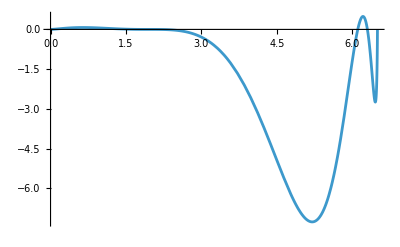

```mathematica
Plot[Det[mat2],{ℰ,0,vpot}]
```

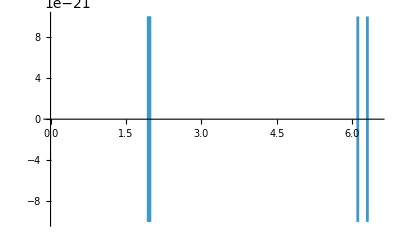

```mathematica
fig = Plot[Det[mat2],{ℰ,0,vpot},PlotRange->{-10^-20,10^-20}]
```

```mathematica
fig[[1,1,1,1,1,3,1]][[2;;-1]]
```

{Line[{{6.1087,-1.×10^-20},{6.1087,1.×10^-20}}],Line[{{6.29986,1.×10^-20},{6.29986,-1.×10^-20}}],Line[{{1.95883,-1.×10^-20},{1.95883,1.×10^-20}}],Line[{{1.94228,1.×10^-20},{1.94228,-1.×10^-20}}],Line[{{1.97574,1.×10^-20},{1.97574,-1.×10^-20}}]}

```mathematica
approxroot=fig[[1,1,1,1,1,3,1]][[2;;-1]]//Map[#[[1,1,1]]&,#]&//Sort
```

{1.94228,1.95883,1.97574,6.1087,6.29986}

```mathematica
rval=approxroot//Map[FindRoot[Det[mat2],{ℰ,#}]&,#]&//Map[ℰ/.#&,#]&
```

{1.94221,1.95883,1.97582,6.10868,6.29988}

```mathematica
fig[[1,1,1]]
```

{{{{},{},{Directive[Opacity[1.],RGBColor[0.24, 0.6, 0.8],AbsoluteThickness[2]],Line[{{6.1087,-1.×10^-20},{6.1087,1.×10^-20}}],Line[{{6.29986,1.×10^-20},{6.29986,-1.×10^-20}}],Line[{{1.95883,-1.×10^-20},{1.95883,1.×10^-20}}],Line[{{1.94228,1.×10^-20},{1.94228,-1.×10^-20}}],Line[{{1.97574,1.×10^-20},{1.97574,-1.×10^-20}}]}}},{}}

### Level 1

```mathematica
nval = 1;
Do[Subscript[c,i]=.,{i,12}];
Evaluate[Table[Subscript[c, i],{i,12}]]=(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

Unset::norep: Assignment on Subscript for c_1 not found.

Unset::norep: Assignment on Subscript for c_2 not found.

Unset::norep: Assignment on Subscript for c_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

{0.707107,0.0000310948,0.000147461,1.97697×10^-7,0.00052956,0.000213445,0,0.00052956,1.97697×10^-7,0.0000310948,-0.000147461,0.707107}

We need to find the normalization constant for φ(x) , ∞

```mathematica
int =NIntegrate[Abs[φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

7.64351×10^-8

```mathematica
1/√int
```

3617.04

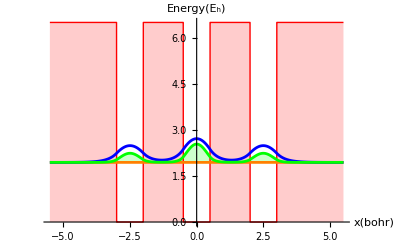

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int) φ[x],
ℰ+(1/(√int) φ[x])^2

}/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,
{x,-5.5,5.5},
PlotRange->All,
AxesLabel->{"x(bohr)","Energy(E_h)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
PlotStyle->{{Red,Thick},Orange, Blue, Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}

]
```

Here we can see the bounding state

For this first energy level we can see that there is no nodes, since we have two atoms the energy level splits, it is forming a bounding level. This is the origin of the covalent bond which is related with the tunneling effect, since in the forbidden region is non zero, so the electron can be found with probabilities to be in the left region or right region. The blue line is the wave function.

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron when x>a+b/2?

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-lb,lb}]
```

0.437291

Let' s find the Δx, then we need the expected value of ⟨x⟩ and ⟨x^2⟩

```mathematica
⟨x⟩=NIntegrate[1/(√int)φ[x]*x 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

-5.47427×10^-8

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)φ[x]*x^2 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

3.21256

Then the Δx is :

```mathematica
Δx = √(⟨x^2⟩-⟨x⟩^2)
```

1.79236

Now let' s find the uncertainty in the momentum Δp :

```mathematica
⟨p⟩=NIntegrate[1/(√int)φ[x]**-ⅈ D[1/(√int)φ[x],x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.50000002690277323972250003402563033483990695415855043393094092608}. NIntegrate obtained 0.-1.0824×10^-10 ⅈ and 1.61219×10^-13 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)φ[x]*(-D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

2.23693

Then Δp is

```mathematica
Δp =  √(⟨p^2⟩-⟨p⟩^2)
```

1.49564

Therefore the Heisengerg uncertainty Δx Δp is:

```mathematica
Δx Δp
```

2.68072

What is the expected value of the kinetic energy k = -ℏ^2/(2m)

```mathematica
⟨Subscript[k, nval]⟩=NIntegrate[1/(√int)φ[x]*(-1/2 D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

1.11847

What is the expected potential energy for this level?

```mathematica
⟨Subscript[U, nval]⟩=NIntegrate[1/(√int)φ[x]*v[x]  1/(√int) φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

0.823743

Now, check this out: The total energy of the level

```mathematica
Subscript[E3, tot1]=⟨Subscript[k, nval]⟩+⟨Subscript[U, nval]⟩
```

1.94221

```mathematica
ℰ/.ℰ->rval[[nval]]
```

1.94221

### Level 2

```mathematica
nval = 2;
Do[Subscript[c,i]=.,{i,12}];
Evaluate[Table[Subscript[c, i],{i,12}]]=(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{-0.707107,-0.000035651,-0.000148341,-2.01996×10^-7,-1.634×10^-6,0,1.52376×10^-6,1.634×10^-6,2.01996×10^-7,0.000035651,-0.000148341,0.707107}

We need to find the normalization constant for φ(x) , ∞

```mathematica
int =NIntegrate[Abs[φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

3.87254×10^-8

```mathematica
1/√int
```

5081.62

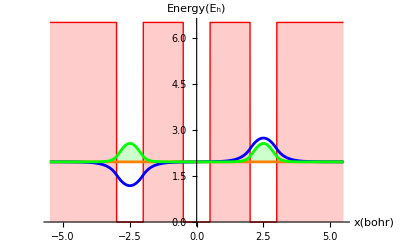

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int) φ[x],
ℰ+(1/(√int) φ[x])^2

}/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,
{x,-5.5,5.5},
PlotRange->All,
AxesLabel->{"x(bohr)","Energy(E_h)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
PlotStyle->{{Red,Thick},Orange, Blue, Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}

]
```

Here we can see the anti-bounding state

For this first energy level we can see that there is no nodes, since we have two atoms the energy level splits, it is forming a bounding level. This is the origin of the covalent bond which is related with the tunneling effect, since in the forbidden region is non zero, so the electron can be found with probabilities to be in the left region or right region. The blue line is the wave function.

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron when x>a+b/2?

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-1,1}]
```

0.000172036

Let' s find the Δx, then we need the expected value of ⟨x⟩ and ⟨x^2⟩

```mathematica
⟨x⟩=NIntegrate[1/(√int)φ[x]*x 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

-2.71113×10^-8

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)φ[x]*x^2 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

6.36

Then the Δx is :

```mathematica
Δx = √(⟨x^2⟩-⟨x⟩^2)
```

2.5219

Now let' s find the uncertainty in the momentum Δp :

```mathematica
⟨p⟩=NIntegrate[1/(√int)φ[x]**-ⅈ D[1/(√int)φ[x],x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-1.9999999730972267602774999659743696651600930458414495660690590739}. NIntegrate obtained 0.+1.48697×10^-10 ⅈ and 1.62464×10^-13 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)φ[x]*(-D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

2.35437

Then Δp is

```mathematica
Δp =  √(⟨p^2⟩-⟨p⟩^2)
```

1.53439

Therefore the Heisengerg uncertainty Δx Δp is:

```mathematica
Δx Δp
```

3.8696

What is the expected value of the kinetic energy k = -ℏ^2/(2m)

```mathematica
⟨Subscript[k, nval]⟩=NIntegrate[1/(√int)φ[x]*(-1/2 D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

1.17718

What is the expected potential energy for this level?

```mathematica
⟨Subscript[U, nval]⟩=NIntegrate[1/(√int)φ[x]*v[x]  1/(√int) φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

0.781646

Now, check this out: The total energy of the level

```mathematica
Subscript[E3, tot2]=⟨Subscript[k, nval]⟩+⟨Subscript[U, nval]⟩
```

1.95883

```mathematica
ℰ/.ℰ->rval[[nval]]
```

1.95883

### Level 3

```mathematica
nval = 3;
Do[Subscript[c,i]=.,{i,12}];
Evaluate[Table[Subscript[c, i],{i,12}]]=(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{0.707107,0.0000403763,0.000149132,2.06494×10^-7,-0.000539562,-0.000218154,0,-0.000539562,2.06494×10^-7,0.0000403763,-0.000149132,0.707107}

We need to find the normalization constant for φ(x) , ∞

```mathematica
int =NIntegrate[Abs[φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

7.84932×10^-8

```mathematica
1/√int
```

3569.31

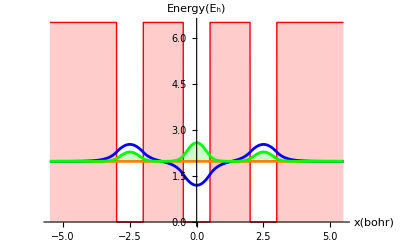

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int) φ[x],
ℰ+(1/(√int) φ[x])^2

}/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,
{x,-5.5,5.5},
PlotRange->All,
AxesLabel->{"x(bohr)","Energy(E_h)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
PlotStyle->{{Red,Thick},Orange, Blue, Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}

]
```

Here we can see the bounding state

For this first energy level we can see that there is no nodes, since we have two atoms the energy level splits, it is forming a bounding level. This is the origin of the covalent bond which is related with the tunneling effect, since in the forbidden region is non zero, so the electron can be found with probabilities to be in the left region or right region. The blue line is the wave function.

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron when x>a+b/2?

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-lb,lb}]
```

0.442584

Let' s find the Δx, then we need the expected value of ⟨x⟩ and ⟨x^2⟩

```mathematica
⟨x⟩=NIntegrate[1/(√int)φ[x]*x 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

1.36352×10^-8

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)φ[x]*x^2 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

3.25905

Then the Δx is :

```mathematica
Δx = √(⟨x^2⟩-⟨x⟩^2)
```

1.80528

Now let' s find the uncertainty in the momentum Δp :

```mathematica
⟨p⟩=NIntegrate[1/(√int)φ[x]**-ⅈ D[1/(√int)φ[x],x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.50000002690277323972250003402563033483990695415855043393094092608}. NIntegrate obtained 0.-6.83246×10^-11 ⅈ and 1.63831×10^-13 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)φ[x]*(-D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

2.47675

Then Δp is

```mathematica
Δp =  √(⟨p^2⟩-⟨p⟩^2)
```

1.57377

Therefore the Heisengerg uncertainty Δx Δp is:

```mathematica
Δx Δp
```

2.8411

What is the expected value of the kinetic energy k = -ℏ^2/(2m)

```mathematica
⟨Subscript[k, nval]⟩=NIntegrate[1/(√int)φ[x]*(-1/2 D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

1.23838

What is the expected potential energy for this level?

```mathematica
⟨Subscript[U, nval]⟩=NIntegrate[1/(√int)φ[x]*v[x]  1/(√int) φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

0.737446

Now, check this out: The total energy of the level

```mathematica
Subscript[E3, tot3]=⟨Subscript[k, nval]⟩+⟨Subscript[U, nval]⟩
```

1.97582

```mathematica
ℰ/.ℰ->rval[[nval]]
```

1.97582

### Level 4

```mathematica
nval = 4;
Do[Subscript[c,i]=.,{i,12}];
Evaluate[Table[Subscript[c, i],{i,12}]]=(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{-0.698479,0.034836,-0.0368388,0.0061005,0.0858131,0,-0.0656567,-0.0858131,-0.0061005,-0.034836,-0.0368388,0.698479}

We need to find the normalization constant for φ(x) , ∞

```mathematica
int =NIntegrate[Abs[φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

0.0156046

```mathematica
1/√int
```

8.00523

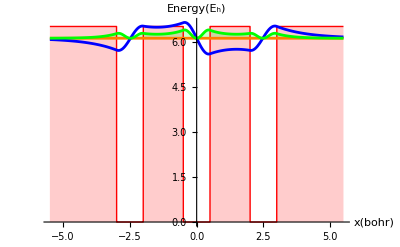

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int) φ[x],
ℰ+(1/(√int) φ[x])^2

}/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,
{x,-5.5,5.5},
PlotRange->All,
AxesLabel->{"x(bohr)","Energy(E_h)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
PlotStyle->{{Red,Thick},Orange, Blue, Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}

]
```

Here we can see the bounding state

For this first energy level we can see that there is no nodes, since we have two atoms the energy level splits, it is forming a bounding level. This is the origin of the covalent bond which is related with the tunneling effect, since in the forbidden region is non zero, so the electron can be found with probabilities to be in the left region or right region. The blue line is the wave function.

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron when x>a+b/2?

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-lb,lb}]
```

0.151816

Let' s find the Δx, then we need the expected value of ⟨x⟩ and ⟨x^2⟩

```mathematica
⟨x⟩=NIntegrate[1/(√int)φ[x]*x 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.999999982064817840184999977316246443440062030560966377379372716}. NIntegrate obtained -1.69413×10^-14 and 9.50808×10^-14 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)φ[x]*x^2 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

4.25206

Then the Δx is :

```mathematica
Δx = √(⟨x^2⟩-⟨x⟩^2)
```

2.06205

Now let' s find the uncertainty in the momentum Δp :

```mathematica
⟨p⟩=NIntegrate[1/(√int)φ[x]**-ⅈ D[1/(√int)φ[x],x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.50000002690277323972250003402563033483990695415855043393094092608}. NIntegrate obtained 0.+2.65413×10^-16 ⅈ and 4.56698×10^-14 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)φ[x]*(-D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

3.54265

Then Δp is

```mathematica
Δp =  √(⟨p^2⟩-⟨p⟩^2)
```

1.88219

Therefore the Heisengerg uncertainty Δx Δp is:

```mathematica
Δx Δp
```

3.88118

What is the expected value of the kinetic energy k = -ℏ^2/(2m)

```mathematica
⟨Subscript[k, nval]⟩=NIntegrate[1/(√int)φ[x]*(-1/2 D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

1.77133

What is the expected potential energy for this level?

```mathematica
⟨Subscript[U, nval]⟩=NIntegrate[1/(√int)φ[x]*v[x]  1/(√int) φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

4.33736

Now, check this out: The total energy of the level

```mathematica
Subscript[E3, tot4]=⟨Subscript[k, nval]⟩+⟨Subscript[U, nval]⟩
```

6.10868

```mathematica
ℰ/.ℰ->rval[[nval]]
```

6.10868

### Level 5

```mathematica
nval = 5;
Do[Subscript[c,i]=.,{i,12}];
Evaluate[Table[Subscript[c, i],{i,12}]]=(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{0.695712,-0.0529129,0.0917521,-0.0337914,0.0590903,0.0162766,0,0.0590903,-0.0337914,-0.0529129,-0.0917521,0.695712}

We need to find the normalization constant for φ(x) , ∞

```mathematica
int =NIntegrate[Abs[φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

0.0395591

```mathematica
1/√int
```

5.02778

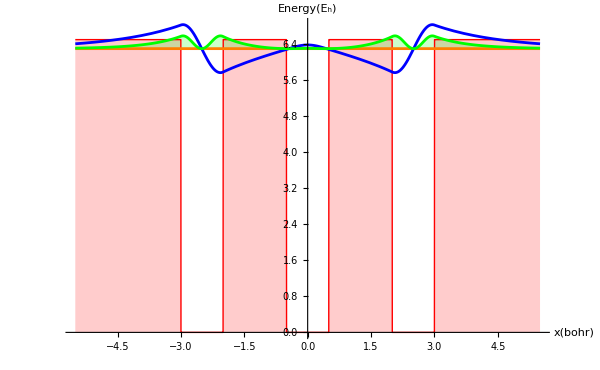

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int) φ[x],
ℰ+(1/(√int) φ[x])^2

}/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,
{x,-5.5,5.5},
PlotRange->All,
AxesLabel->{"x(bohr)","Energy(E_h)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
PlotStyle->{{Red,Thick},Orange, Blue, Green},
Exclusions->None,
ImageSize->600,
Filling->{1->Axis,4->rval[[nval]]}
]
```

Here we can see the bounding state

For this first energy level we can see that there is no nodes, since we have two atoms the energy level splits, it is forming a bounding level. This is the origin of the covalent bond which is related with the tunneling effect, since in the forbidden region is non zero, so the electron can be found with probabilities to be in the left region or right region. The blue line is the wave function.

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron when x>a+b/2?

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-lb,lb}]
```

0.0029742

Let' s find the Δx, then we need the expected value of ⟨x⟩ and ⟨x^2⟩

```mathematica
⟨x⟩=NIntegrate[1/(√int)φ[x]*x 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.9999999730972267602774999659743696651600930458414495660690590739}. NIntegrate obtained 3.93401×10^-14 and 1.45035×10^-13 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)φ[x]*x^2 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

9.19688

Then the Δx is :

```mathematica
Δx = √(⟨x^2⟩-⟨x⟩^2)
```

3.03264

Now let' s find the uncertainty in the momentum Δp :

```mathematica
⟨p⟩=NIntegrate[1/(√int)φ[x]**-ⅈ D[1/(√int)φ[x],x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.9999999730972267602774999659743696651600930458414495660690590739}. NIntegrate obtained 0.+2.10769×10^-15 ⅈ and 6.26468×10^-14 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)φ[x]*(-D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

3.73646

Then Δp is

```mathematica
Δp =  √(⟨p^2⟩-⟨p⟩^2)
```

1.93299

Therefore the Heisengerg uncertainty Δx Δp is:

```mathematica
Δx Δp
```

5.86206

What is the expected value of the kinetic energy k = -ℏ^2/(2m)

```mathematica
⟨Subscript[k, nval]⟩=NIntegrate[1/(√int)φ[x]*(-1/2 D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

1.86823

What is the expected potential energy for this level?

```mathematica
⟨Subscript[U, nval]⟩=NIntegrate[1/(√int)φ[x]*v[x]  1/(√int) φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

4.43165

Now, check this out: The total energy of the level

```mathematica
Subscript[E3, tot5]=⟨Subscript[k, nval]⟩+⟨Subscript[U, nval]⟩
```

6.29988

```mathematica
ℰ/.ℰ->rval[[nval]]
```

6.29988

### Level 6

```mathematica
nval = 6;
Do[Subscript[c,i]=.,{i,12}];
Evaluate[Table[Subscript[c, i],{i,12}]]=(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

Part::partw: Part 6 of {1.94221,1.95883,1.97582,6.10868,6.29988} does not exist.

Part::partw: Part 1 of {} does not exist.

Set::shape: Lists {c_1,c_2,c_3,c_4,c_5,c_6,c_7,c_8,c_9,c_10,c_11,c_12} and {}⟦1⟧ are not the same shape.

{}⟦1⟧

We need to find the normalization constant for φ(x) , ∞

```mathematica
int =NIntegrate[Abs[φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

Part::partw: Part 6 of {1.94221,1.95883,1.97582,6.10868,6.29988} does not exist.

NIntegrate::inumr: The integrand Abs[{ | «1»]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}]

```mathematica
1/√int
```

NIntegrate::inumr: The integrand Abs[{ | «1»]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

1/(√NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}])

NIntegrate::inumr: The integrand Abs[{ | «1»]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Part::partw: Part 6 of {1.94221,1.95883,1.97582,6.10868,6.29988} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Filling::invfillentry: {1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧ is not a valid Filling specification.

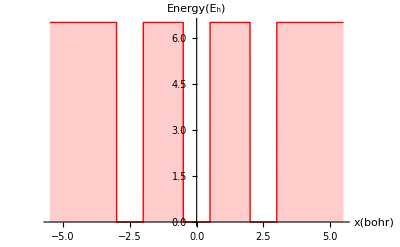

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int) φ[x],
ℰ+(1/(√int) φ[x])^2

}/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,
{x,-5.5,5.5},
PlotRange->All,
AxesLabel->{"x(bohr)","Energy(E_h)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
PlotStyle->{{Red,Thick},Orange, Blue, Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}

]
```

Here we can see the bounding state

For this first energy level we can see that there is no nodes, since we have two atoms the energy level splits, it is forming a bounding level. This is the origin of the covalent bond which is related with the tunneling effect, since in the forbidden region is non zero, so the electron can be found with probabilities to be in the left region or right region. The blue line is the wave function.

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

NIntegrate::inumr: The integrand Abs[{ | «1»]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Part::partw: Part 6 of {1.94221,1.95883,1.97582,6.10868,6.29988} does not exist.

NIntegrate::write: Tag Times in -x is Protected.

NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]/(√NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}])]^2,{x,-∞,∞}]

What is the probability of finding one electron when x>a+b/2?

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-lb,lb}]
```

NIntegrate::inumr: The integrand Abs[{ | «1»]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Part::partw: Part 6 of {1.94221,1.95883,1.97582,6.10868,6.29988} does not exist.

NIntegrate::write: Tag Times in -x is Protected.

NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]/(√NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}])]^2,{x,-lb,lb}]

Let' s find the Δx, then we need the expected value of ⟨x⟩ and ⟨x^2⟩

```mathematica
⟨x⟩=NIntegrate[1/(√int)φ[x]*x 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::inumr: The integrand Abs[{ | «1»]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Part::partw: Part 6 of {1.94221,1.95883,1.97582,6.10868,6.29988} does not exist.

NIntegrate::write: Tag Times in -x is Protected.

General::stop: Further output of NIntegrate::write will be suppressed during this calculation.

NIntegrate[(x Conjugate[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]] (Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]))/NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}],{x,-∞,∞}]

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)φ[x]*x^2 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::inumr: The integrand Abs[{ | «1»]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Part::partw: Part 6 of {1.94221,1.95883,1.97582,6.10868,6.29988} does not exist.

NIntegrate::write: Tag Times in -x is Protected.

General::stop: Further output of NIntegrate::write will be suppressed during this calculation.

NIntegrate[(x^2 Conjugate[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]] (Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]))/NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}],{x,-∞,∞}]

Then the Δx is :

```mathematica
Δx = √(⟨x^2⟩-⟨x⟩^2)
```

NIntegrate::inumr: The integrand Abs[{ | «1»]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

NIntegrate::write: Tag Times in -x is Protected.

NIntegrate::inumr: The integrand Abs[{ | «1»]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::write: Tag Times in -x is Protected.

General::stop: Further output of NIntegrate::write will be suppressed during this calculation.

√(-(NIntegrate[(x Conjugate[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]] (Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]))/NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}],{x,-∞,∞}])^2+NIntegrate[(x^2 Conjugate[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]] (Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]))/NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}],{x,-∞,∞}])

Now let' s find the uncertainty in the momentum Δp :

```mathematica
⟨p⟩=NIntegrate[1/(√int)φ[x]**-ⅈ D[1/(√int)φ[x],x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

NIntegrate::inumr: The integrand Abs[{ | «1»]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Part::partw: Part 6 of {1.94221,1.95883,1.97582,6.10868,6.29988} does not exist.

NIntegrate::write: Tag Times in -x is Protected.

D::ivar: -x is not a valid variable.

NIntegrate::write: Tag Times in -x is Protected.

General::stop: Further output of NIntegrate::write will be suppressed during this calculation.

D::ivar: -x is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

NIntegrate[-((ⅈ Conjugate[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]] (-((∂_x NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}] (Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]))/(2 NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}]^(3/2)))+Piecewise[{{√2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_1, 3.+x<0}, {-√2 √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+√2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_3, 3.+x≥0&&2+x≤0}, {-√2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_4+√2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_5, 2+x≥0&&0.5+x≤0}, {-√2 √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+√2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_7, 0.5+x≥0&&0.5-x≥0}, {-√2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_8+√2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_9, 0.5-x≤0&&2-x≥0}, {-√2 √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+√2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_11, 2-x≤0&&3.-x≥0}, {-√2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_12, 3.-x<0}, {0, True}}]/(√NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}])))/(√NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}])),{x,-∞,∞}]

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)φ[x]*(-D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::inumr: The integrand Abs[{ | «1»]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Part::partw: Part 6 of {1.94221,1.95883,1.97582,6.10868,6.29988} does not exist.

NIntegrate::write: Tag Times in -x is Protected.

D::ivar: -x is not a valid variable.

NIntegrate::write: Tag Times in -x is Protected.

General::stop: Further output of NIntegrate::write will be suppressed during this calculation.

D::ivar: -x is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

NIntegrate[(Conjugate[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]] (-(((3 (∂_x NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}])^2)/(4 NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}]^(5/2))-∂_{x,2} NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}]/(2 NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}]^(3/2))) (Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]))+(∂_x NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}] (Piecewise[{{√2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_1, 3.+x<0}, {-√2 √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+√2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_3, 3.+x≥0&&2+x≤0}, {-√2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_4+√2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_5, 2+x≥0&&0.5+x≤0}, {-√2 √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+√2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_7, 0.5+x≥0&&0.5-x≥0}, {-√2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_8+√2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_9, 0.5-x≤0&&2-x≥0}, {-√2 √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+√2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_11, 2-x≤0&&3.-x≥0}, {-√2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_12, 3.-x<0}, {0, True}}]))/NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}]^(3/2)-Piecewise[{{2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) (6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_1, 3.+x<0}, {-2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] {1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧ c_2-2 {1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧ Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, 3.+x≥0&&2+x≤0}, {2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) (6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_4+2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) (6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_5, 2+x≥0&&0.5+x≤0}, {-2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] {1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧ c_6-2 {1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧ Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, 0.5+x≥0&&0.5-x≥0}, {2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) (6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_8+2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) (6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_9, 0.5-x≤0&&2-x≥0}, {-2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] {1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧ c_10-2 {1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧ Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2-x≤0&&3.-x≥0}, {2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) (6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_12, 3.-x<0}, {0, True}}]/(√NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}])))/(√NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}]),{x,-∞,∞}]

Then Δp is

```mathematica
Δp =  √(⟨p^2⟩-⟨p⟩^2)
```

NIntegrate::inumr: The integrand Abs[{ | «1»]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::write: Tag Times in -x is Protected.

D::ivar: -x is not a valid variable.

NIntegrate::write: Tag Times in -x is Protected.

General::stop: Further output of NIntegrate::write will be suppressed during this calculation.

D::ivar: -x is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

√(-(NIntegrate[-((ⅈ Conjugate[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]] (-((∂_x NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}] (Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]))/(2 NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}]^(3/2)))+Piecewise[{{√2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_1, 3.+x<0}, {-√2 √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+√2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_3, 3.+x≥0&&2+x≤0}, {-√2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_4+√2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_5, 2+x≥0&&0.5+x≤0}, {-√2 √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+√2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_7, 0.5+x≥0&&0.5-x≥0}, {-√2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_8+√2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_9, 0.5-x≤0&&2-x≥0}, {-√2 √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+√2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_11, 2-x≤0&&3.-x≥0}, {-√2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_12, 3.-x<0}, {0, True}}]/(√NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}])))/(√NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}])),{x,-∞,∞}])^2+NIntegrate[(Conjugate[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]] (-(((3 (∂_x NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}])^2)/(4 NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}]^(5/2))-∂_{x,2} NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}]/(2 NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}]^(3/2))) (Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]))+(∂_x NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}] (Piecewise[{{√2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_1, 3.+x<0}, {-√2 √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+√2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_3, 3.+x≥0&&2+x≤0}, {-√2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_4+√2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_5, 2+x≥0&&0.5+x≤0}, {-√2 √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+√2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_7, 0.5+x≥0&&0.5-x≥0}, {-√2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_8+√2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_9, 0.5-x≤0&&2-x≥0}, {-√2 √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+√2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_11, 2-x≤0&&3.-x≥0}, {-√2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_12, 3.-x<0}, {0, True}}]))/NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}]^(3/2)-Piecewise[{{2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) (6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_1, 3.+x<0}, {-2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] {1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧ c_2-2 {1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧ Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, 3.+x≥0&&2+x≤0}, {2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) (6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_4+2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) (6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_5, 2+x≥0&&0.5+x≤0}, {-2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] {1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧ c_6-2 {1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧ Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, 0.5+x≥0&&0.5-x≥0}, {2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) (6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_8+2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) (6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_9, 0.5-x≤0&&2-x≥0}, {-2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] {1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧ c_10-2 {1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧ Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2-x≤0&&3.-x≥0}, {2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) (6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_12, 3.-x<0}, {0, True}}]/(√NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}])))/(√NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}]),{x,-∞,∞}])

Therefore the Heisengerg uncertainty Δx Δp is:

```mathematica
Δx Δp
```

NIntegrate::inumr: The integrand Abs[{ | «1»]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

NIntegrate::write: Tag Times in -x is Protected.

NIntegrate::inumr: The integrand Abs[{ | «1»]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::write: Tag Times in -x is Protected.

General::stop: Further output of NIntegrate::write will be suppressed during this calculation.

D::ivar: -x is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

√(-(NIntegrate[(x Conjugate[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]] (Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]))/NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}],{x,-∞,∞}])^2+NIntegrate[(x^2 Conjugate[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]] (Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]))/NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}],{x,-∞,∞}]) √(-(NIntegrate[-((ⅈ Conjugate[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]] (-((∂_x NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}] (Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]))/(2 NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}]^(3/2)))+Piecewise[{{√2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_1, 3.+x<0}, {-√2 √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+√2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_3, 3.+x≥0&&2+x≤0}, {-√2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_4+√2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_5, 2+x≥0&&0.5+x≤0}, {-√2 √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+√2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_7, 0.5+x≥0&&0.5-x≥0}, {-√2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_8+√2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_9, 0.5-x≤0&&2-x≥0}, {-√2 √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+√2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_11, 2-x≤0&&3.-x≥0}, {-√2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_12, 3.-x<0}, {0, True}}]/(√NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}])))/(√NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}])),{x,-∞,∞}])^2+NIntegrate[(Conjugate[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]] (-(((3 (∂_x NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}])^2)/(4 NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}]^(5/2))-∂_{x,2} NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}]/(2 NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}]^(3/2))) (Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]))+(∂_x NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}] (Piecewise[{{√2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_1, 3.+x<0}, {-√2 √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+√2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_3, 3.+x≥0&&2+x≤0}, {-√2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_4+√2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_5, 2+x≥0&&0.5+x≤0}, {-√2 √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+√2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_7, 0.5+x≥0&&0.5-x≥0}, {-√2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_8+√2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_9, 0.5-x≤0&&2-x≥0}, {-√2 √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+√2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_11, 2-x≤0&&3.-x≥0}, {-√2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_12, 3.-x<0}, {0, True}}]))/NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}]^(3/2)-Piecewise[{{2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) (6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_1, 3.+x<0}, {-2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] {1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧ c_2-2 {1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧ Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, 3.+x≥0&&2+x≤0}, {2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) (6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_4+2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) (6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_5, 2+x≥0&&0.5+x≤0}, {-2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] {1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧ c_6-2 {1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧ Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, 0.5+x≥0&&0.5-x≥0}, {2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) (6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_8+2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) (6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_9, 0.5-x≤0&&2-x≥0}, {-2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] {1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧ c_10-2 {1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧ Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2-x≤0&&3.-x≥0}, {2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) (6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_12, 3.-x<0}, {0, True}}]/(√NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}])))/(√NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}]),{x,-∞,∞}])

What is the expected value of the kinetic energy k = -ℏ^2/(2m)

```mathematica
⟨Subscript[k, nval]⟩=NIntegrate[1/(√int)φ[x]*(-1/2 D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::inumr: The integrand Abs[{ | «1»]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Part::partw: Part 6 of {1.94221,1.95883,1.97582,6.10868,6.29988} does not exist.

NIntegrate::write: Tag Times in -x is Protected.

D::ivar: -x is not a valid variable.

NIntegrate::write: Tag Times in -x is Protected.

General::stop: Further output of NIntegrate::write will be suppressed during this calculation.

D::ivar: -x is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

NIntegrate[(Conjugate[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]] (-(((3 (∂_x NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}])^2)/(4 NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}]^(5/2))-∂_{x,2} NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}]/(2 NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}]^(3/2))) (Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]))+(∂_x NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}] (Piecewise[{{√2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_1, 3.+x<0}, {-√2 √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+√2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_3, 3.+x≥0&&2+x≤0}, {-√2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_4+√2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_5, 2+x≥0&&0.5+x≤0}, {-√2 √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+√2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_7, 0.5+x≥0&&0.5-x≥0}, {-√2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_8+√2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_9, 0.5-x≤0&&2-x≥0}, {-√2 √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+√2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_11, 2-x≤0&&3.-x≥0}, {-√2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_12, 3.-x<0}, {0, True}}]))/NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}]^(3/2)-Piecewise[{{2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) (6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_1, 3.+x<0}, {-2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] {1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧ c_2-2 {1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧ Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, 3.+x≥0&&2+x≤0}, {2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) (6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_4+2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) (6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_5, 2+x≥0&&0.5+x≤0}, {-2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] {1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧ c_6-2 {1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧ Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, 0.5+x≥0&&0.5-x≥0}, {2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) (6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_8+2 ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) (6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_9, 0.5-x≤0&&2-x≥0}, {-2 Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] {1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧ c_10-2 {1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧ Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2-x≤0&&3.-x≥0}, {2 ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) (6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧) c_12, 3.-x<0}, {0, True}}]/(√NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}])))/(2 √NIntegrate[Abs[Piecewise[{{ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_1, x<-3.}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_2+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_3, -3.≤x≤-2}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_4+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_5, -2≤x≤-0.5}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_6+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_7, -0.5≤x≤0.5}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_8+ⅇ^(√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_9, 0.5≤x≤2}, {Cos[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_10+Sin[√2 x √({1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)] c_11, 2≤x≤3.}, {ⅇ^(-√2 x √(6.5-{1.94221,1.95883,1.97582,6.10868,6.29988}⟦6⟧)) c_12, x>3.}, {0, True}}]]^2,{x,-∞,∞}]),{x,-∞,∞}]

What is the expected potential energy for this level?

```mathematica
⟨Subscript[U, nval]⟩=NIntegrate[1/(√int)φ[x]*v[x]  1/(√int) φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::inumr: The integrand Abs[{ | «1»]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Part::partw: Part 6 of {1.94221,1.95883,1.97582,6.10868,6.29988} does not exist.

NIntegrate::write: Tag Times in -x is Protected.

$Aborted

Now, check this out: The total energy of the level

```mathematica
Subscript[E3, tot6]=⟨Subscript[k, nval]⟩+⟨Subscript[U, nval]⟩
```

1.6543

```mathematica
ℰ/.ℰ->rval[[nval]]
```

1.6543

### Level 7

```mathematica
nval = 7;
Do[Subscript[c,i]=.,{i,12}];
Evaluate[Table[Subscript[c, i],{i,12}]]=(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{0.707107,1.55954×10^-6,1.77901×10^-6,8.63507×10^-9,0.000108904,-3.23693×10^-6,0,0.000108904,8.63507×10^-9,1.55954×10^-6,-1.77901×10^-6,0.707107}

We need to find the normalization constant for φ(x) , ∞

```mathematica
int =NIntegrate[Abs[φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

4.19725×10^-11

```mathematica
1/√int
```

154354.

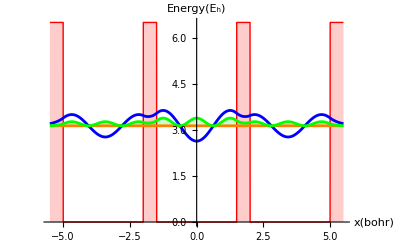

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int) φ[x],
ℰ+(1/(√int) φ[x])^2

}/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,
{x,-5.5,5.5},
PlotRange->All,
AxesLabel->{"x(bohr)","Energy(E_h)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
PlotStyle->{{Red,Thick},Orange, Blue, Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}

]
```

Here we can see the bounding state

For this first energy level we can see that there is no nodes, since we have two atoms the energy level splits, it is forming a bounding level. This is the origin of the covalent bond which is related with the tunneling effect, since in the forbidden region is non zero, so the electron can be found with probabilities to be in the left region or right region. The blue line is the wave function.

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron when x>a+b/2?

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-lb,lb}]
```

0.421401

Let' s find the Δx, then we need the expected value of ⟨x⟩ and ⟨x^2⟩

```mathematica
⟨x⟩=NIntegrate[1/(√int)φ[x]*x 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

-2.19207×10^-8

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)φ[x]*x^2 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

7.31154

Then the Δx is :

```mathematica
Δx = √(⟨x^2⟩-⟨x⟩^2)
```

2.70399

Now let' s find the uncertainty in the momentum Δp :

```mathematica
⟨p⟩=NIntegrate[1/(√int)φ[x]**-ⅈ D[1/(√int)φ[x],x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)φ[x]*(-D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

4.55335

Then Δp is

```mathematica
Δp =  √(⟨p^2⟩-⟨p⟩^2)
```

2.13386

Therefore the Heisengerg uncertainty Δx Δp is:

```mathematica
Δx Δp
```

5.76992

What is the expected value of the kinetic energy k = -ℏ^2/(2m)

```mathematica
⟨Subscript[k, nval]⟩=NIntegrate[1/(√int)φ[x]*(-1/2 D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

2.27668

What is the expected potential energy for this level?

```mathematica
⟨Subscript[U, nval]⟩=NIntegrate[1/(√int)φ[x]*v[x]  1/(√int) φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

0.857598

Now, check this out: The total energy of the level

```mathematica
Subscript[E3, tot7]=⟨Subscript[k, nval]⟩+⟨Subscript[U, nval]⟩
```

3.13427

```mathematica
ℰ/.ℰ->rval[[nval]]
```

3.13427

### Level 8

```mathematica
nval = 8;
Do[Subscript[c,i]=.,{i,12}];
Evaluate[Table[Subscript[c, i],{i,12}]]=(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{-0.707107,-3.59726×10^-6,-1.14039×10^-6,-1.86216×10^-8,1.38369×10^-6,0,-1.08398×10^-6,-1.38369×10^-6,1.86216×10^-8,3.59726×10^-6,-1.14039×10^-6,0.707107}

We need to find the normalization constant for φ(x) , ∞

```mathematica
int =NIntegrate[Abs[φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

5.5387×10^-11

```mathematica
1/√int
```

134368.

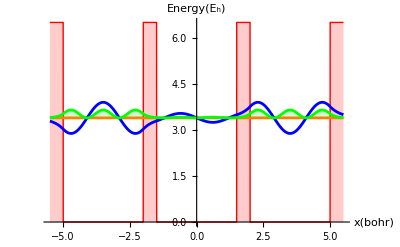

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int) φ[x],
ℰ+(1/(√int) φ[x])^2

}/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,
{x,-5.5,5.5},
PlotRange->All,
AxesLabel->{"x(bohr)","Energy(E_h)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
PlotStyle->{{Red,Thick},Orange, Blue, Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}

]
```

Here we can see the bounding state

For this first energy level we can see that there is no nodes, since we have two atoms the energy level splits, it is forming a bounding level. This is the origin of the covalent bond which is related with the tunneling effect, since in the forbidden region is non zero, so the electron can be found with probabilities to be in the left region or right region. The blue line is the wave function.

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron when x>a+b/2?

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-lb,lb}]
```

0.0277525

Let' s find the Δx, then we need the expected value of ⟨x⟩ and ⟨x^2⟩

```mathematica
⟨x⟩=NIntegrate[1/(√int)φ[x]*x 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

2.4098×10^-8

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)φ[x]*x^2 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

13.0914

Then the Δx is :

```mathematica
Δx = √(⟨x^2⟩-⟨x⟩^2)
```

3.61821

Now let' s find the uncertainty in the momentum Δp :

```mathematica
⟨p⟩=NIntegrate[1/(√int)φ[x]**-ⅈ D[1/(√int)φ[x],x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)φ[x]*(-D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

5.45433

Then Δp is

```mathematica
Δp =  √(⟨p^2⟩-⟨p⟩^2)
```

2.33545

Therefore the Heisengerg uncertainty Δx Δp is:

```mathematica
Δx Δp
```

8.45014

What is the expected value of the kinetic energy k = -ℏ^2/(2m)

```mathematica
⟨Subscript[k, nval]⟩=NIntegrate[1/(√int)φ[x]*(-1/2 D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

2.72716

What is the expected potential energy for this level?

```mathematica
⟨Subscript[U, nval]⟩=NIntegrate[1/(√int)φ[x]*v[x]  1/(√int) φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

0.664771

Now, check this out: The total energy of the level

```mathematica
Subscript[E3, tot8]=⟨Subscript[k, nval]⟩+⟨Subscript[U, nval]⟩
```

3.39193

```mathematica
ℰ/.ℰ->rval[[nval]]
```

3.39193

### Level 9

```mathematica
nval = 9;
Do[Subscript[c,i]=.,{i,12}];
Evaluate[Table[Subscript[c, i],{i,12}]]=(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{0.707107,6.37271×10^-6,-1.95265×10^-6,4.2285×10^-8,-0.000242435,9.12791×10^-6,0,-0.000242435,4.2285×10^-8,6.37271×10^-6,1.95265×10^-6,0.707107}

We need to find the normalization constant for φ(x) , ∞

```mathematica
int =NIntegrate[Abs[φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

3.04571×10^-10

```mathematica
1/√int
```

57300.1

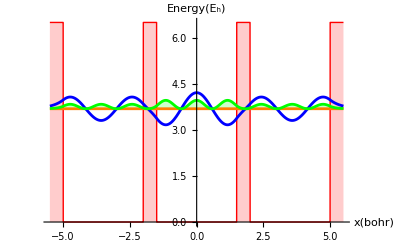

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int) φ[x],
ℰ+(1/(√int) φ[x])^2

}/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,
{x,-5.5,5.5},
PlotRange->All,
AxesLabel->{"x(bohr)","Energy(E_h)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
PlotStyle->{{Red,Thick},Orange, Blue, Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}

]
```

Here we can see the bounding state

For this first energy level we can see that there is no nodes, since we have two atoms the energy level splits, it is forming a bounding level. This is the origin of the covalent bond which is related with the tunneling effect, since in the forbidden region is non zero, so the electron can be found with probabilities to be in the left region or right region. The blue line is the wave function.

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron when x>a+b/2?

```mathematica
NIntegrate[Abs[1/(√int) φ[x]]^2/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-lb,lb}]
```

0.458525

Let' s find the Δx, then we need the expected value of ⟨x⟩ and ⟨x^2⟩

```mathematica
⟨x⟩=NIntegrate[1/(√int)φ[x]*x 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

2.22142×10^-9

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)φ[x]*x^2 1/(√int)φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

7.86428

Then the Δx is :

```mathematica
Δx = √(⟨x^2⟩-⟨x⟩^2)
```

2.80433

Now let' s find the uncertainty in the momentum Δp :

```mathematica
⟨p⟩=NIntegrate[1/(√int)φ[x]**-ⅈ D[1/(√int)φ[x],x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.0000000538055464794450000680512606696798139083171008678618818522}. NIntegrate obtained 0.-4.19382×10^-11 ⅈ and 1.39425×10^-13 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)φ[x]*(-D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

6.63447

Then Δp is

```mathematica
Δp =  √(⟨p^2⟩-⟨p⟩^2)
```

2.57575

Therefore the Heisengerg uncertainty Δx Δp is:

```mathematica
Δx Δp
```

7.22325

What is the expected value of the kinetic energy k = -ℏ^2/(2m)

```mathematica
⟨Subscript[k, nval]⟩=NIntegrate[1/(√int)φ[x]*(-1/2 D[1/(√int)φ[x],{x,2}])/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

3.31724

What is the expected potential energy for this level?

```mathematica
⟨Subscript[U, nval]⟩=NIntegrate[1/(√int)φ[x]*v[x]  1/(√int) φ[x]/.{α -> √(2 (v0-ℰ)) , β->√(2 ℰ)}/.{v0->vpot, a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]//Chop
```

0.371819

Now, check this out: The total energy of the level

```mathematica
Subscript[E3, tot9]=⟨Subscript[k, nval]⟩+⟨Subscript[U, nval]⟩
```

3.68906

```mathematica
ℰ/.ℰ->rval[[nval]]
```

3.68906

### Summary of the plots

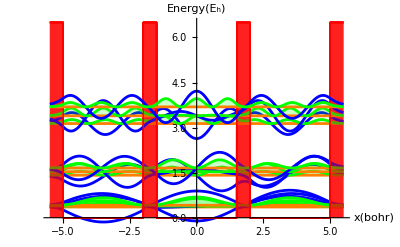

```mathematica
Show@@Table[figure[i],{i,9}]
```

What is the total energy of the system if it has 6 ⅇ?

What is the total energy of the system if it has 6 ⅇ

```mathematica
Etot6e[mol] = 2*(Subscript[E3, tot1]+Subscript[E3, tot2]+Subscript[E3, tot3])
```

2.31719

Kinetic energy of 6 ⅇ

```mathematica
Subscript[k, tot] =2(⟨Subscript[k, 1]⟩+⟨Subscript[k, 2]⟩+⟨Subscript[k, 3]⟩)
```

2.06835

Total potential energy of 6 ⅇ

```mathematica
Subscript[u, tot]=2 (⟨Subscript[U, 1]⟩+⟨Subscript[U, 2]⟩+⟨Subscript[U, 3]⟩)
```

0.248842

### Cohesion Energy

What is the cohesion energy for this 6 ⅇ system,  the cohesion energy is the energy needed to vaporize the system E_cohesion= Emol/2-Eatom.  What is the formation energy?

```mathematica
Subscript[E, cohesion6]=Etot6e[mol]/2-Subscript[E, tot][atom](*this Etot is for the single atom = 4,40221*)
```

1.1586-ⅇ_tot[atom]

Now what would be the cohesion energy if each atom contributes with 4 ⅇ, then the molecule will have 8 ⅇ.

```mathematica
Subscript[E2, tot][atom]= 2(Subscript[E1, tot1]+Subscript[E1, tot2])
```

2 (E1_tot1+E1_tot2)

```mathematica
Etot8e[mol] = 2*(Subscript[E3, tot1]+Subscript[E3, tot2]+Subscript[E3, tot3]+Subscript[E3, tot4])
```

5.14717

```mathematica
Subscript[E, cohesion8]=Etot8e[mol]/2-Subscript[E2, tot][atom]
```

2.57358-2 (E1_tot1+E1_tot2)

Here we notice that  the system evaporates because the cohesion energy is positive meaning that E_atom< E_mol

Now what would be the cohesion energy if each atom contributes with 5 ⅇ, then the molecule will have 10 electrons

```mathematica
Subscript[E3, tot][atom]= 2(Subscript[E1, tot1]+Subscript[E1, tot2])+Subscript[E1, tot3]
```

2 (E1_tot1+E1_tot2)+E1_tot3

```mathematica
Etot10e[mol] = 2*(Subscript[E3, tot1]+Subscript[E3, tot2]+Subscript[E3, tot3]+Subscript[E3, tot4]+Subscript[E3, tot5])
```

8.21016

```mathematica
Subscript[E, cohesion10]=Etot10e[mol]/2-Subscript[E3, tot][atom]
```

4.10508-2 (E1_tot1+E1_tot2)-E1_tot3

Now we observe that the molecule is more stable.